# Bosonic Complexity of Purification (BCoP)

```mathematica
Quit[];
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
SetDirectory[NotebookDirectory[]];
<<GaussianOptimization`
```

## Bosons on a Periodic Lattice

Definitions

The following definitions are equivalent to the previousely used definitions in the Mathematica notebook

```mathematica
FourierMatrixElement[N_]:=Function[{k,x},Exp[I 2 Pi x k /N]/Sqrt[N]];
DispersionRelation[m_,N_,l_]:=Function[{k},Sqrt[m^2+4/l^2  (Sin[Pi k/N])^2]];
```

```mathematica
FT[n_]:=Module[{f,pos,val},
f=FourierMatrixElement[n];
pos=Table[{x,k},{k,n},{x,n}]//Flatten[#,1]&;
val=Table[f[k,x]//N,{k,n},{x,n}]//Flatten[#,1]&;
SparseArray[pos->val]];
```

```mathematica
Diag[m_,n_,l_]:=Module[{ω},
ω=DispersionRelation[m,n,l];
DiagonalMatrix[Table[ω[k],{k,n}]]];
```

```mathematica
invDiag[m_,n_,l_]:=Module[{ω},
ω=DispersionRelation[m,n,l];
DiagonalMatrix[Table[1/ω[k],{k,n}]]];
```

```mathematica
CM[N_,m_,l_]:=Module[{F,D,invD,G,Tr},
F=FT[N];D=Diag[m,N,l]; invD=invDiag[m,N,l];
G=ArrayFlatten[({{F.D.ConjugateTranspose[F], 0}, {0, F.invD.ConjugateTranspose[F]}})]//Chop//SparseArray];
```

```mathematica
partialCM[N_,m_,l_,d_,dim1_,dim2_]:=
Module[{dim, halfdim, bigCM, indices1, indices2,indices, partialCM, Tr},

bigCM=CM[N,m,l];
dim=Length[bigCM]; halfdim=dim/2;

indices1=Thread[{Table[x,{x,dim1}],Table[x+halfdim,{x,dim1}]}]//Flatten[#,1]&;
indices2=Thread[{Table[dim1+d+x,{x,dim2}],Table[dim1+d+x+halfdim,{x,dim2}]}]//Flatten[#,1]&;

indices=Join[indices1,indices2];

partialCM=bigCM[[indices,indices]]];
```

Scenario 1: BCoP as a Function of Subsystem Partition Separation (Fixed Bipartite Subsystem Size) with m=1/10:

## Case 1: N=100, m=1/10, δ=1 ; (N-1)δ == L=99

### Case 1.1: N=100, m=1/10, δ=1, dimS=1

#### Case 1.1.1: N=100, m=1/10, δ=1, dimS=1, l=0

```mathematica
CM0=partialCM[100,1/10,1,0,1,1];CM0//MatrixForm
```

(1.28101 | 0 | -0.41982 | 0
0 | 1.39418 | 0 | 0.760649
-0.41982 | 0 | 1.28101 | 0
0 | 0.760649 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,2,"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[8],"qpqp","qpqp"]
```

{{0.413685,0.137482},{{0.,0.56222,0.,0.56222},{-0.889332,0.,-0.889332,0.},{0.552411,0.,-0.552411,0.},{0.,0.905123,0.,-0.905123}}}

SparseArray[…]

{{0,-1,0,0,0,0,0,0},{1,0,0,0,0,0,0,0},{0,0,0,-1,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,0,0,-1,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,-1},{0,0,0,0,0,0,1,0}}

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4,"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(1+1),(1+1)},10^-9,∞];
```

Final value: 0.707459

Number of iterations: 8

Number of total corrections: 0

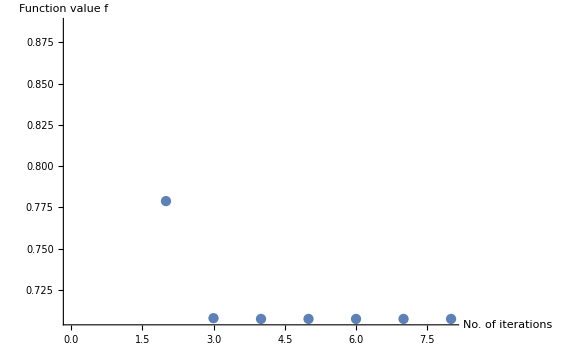

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

0.707459

#### Case 1.1.2: N=100, m=1/10, δ=1, dimS=1, l=1

```mathematica
CM0=partialCM[100,1/10,1,1,1,1];CM0//MatrixForm
```

(1.28101 | 0 | -0.0813337 | 0
0 | 1.39418 | 0 | 0.554542
-0.0813337 | 0 | 1.28101 | 0
0 | 0.554542 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,2,"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[8],"qpqp","qpqp"]
```

{{0.493961,0.185378},{{0.,0.626344,0.,0.626344},{-0.798283,0.,-0.798283,0.},{0.626523,0.,-0.626523,0.},{0.,0.798056,0.,-0.798056}}}

SparseArray[…]

{{0,-1,0,0,0,0,0,0},{1,0,0,0,0,0,0,0},{0,0,0,-1,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,0,0,-1,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,-1},{0,0,0,0,0,0,1,0}}

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4,"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(1+1),(1+1)},10^-9,∞];
```

Final value: 0.767223

Number of iterations: 10

Number of total corrections: 0

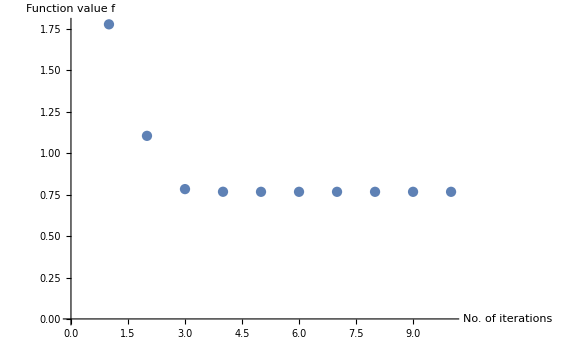

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

0.767223

#### Case 1.1.3: N=100, m=1/10, δ=1, dimS=1, l=2

```mathematica
CM0=partialCM[100,1/10,1,2,1,1];CM0//MatrixForm
```

(1.28101 | 0 | -0.0334432 | 0
0 | 1.39418 | 0 | 0.435315
-0.0334432 | 0 | 1.28101 | 0
0 | 0.435315 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,2,"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[8],"qpqp","qpqp"]
```

{{0.485996,0.245193},{{0.,0.642566,0.,0.642566},{-0.77813,0.,-0.77813,0.},{0.653489,0.,-0.653489,0.},{0.,0.765123,0.,-0.765123}}}

SparseArray[…]

{{0,-1,0,0,0,0,0,0},{1,0,0,0,0,0,0,0},{0,0,0,-1,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,0,0,-1,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,-1},{0,0,0,0,0,0,1,0}}

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4,"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(1+1),(1+1)},10^-9,∞];
```

Final value: 0.780635

Number of iterations: 9

Number of total corrections: 0

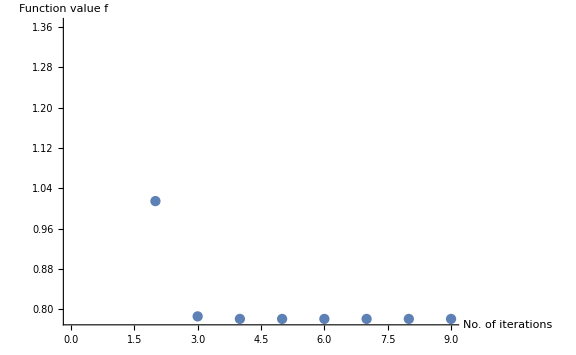

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

0.780635

#### Case 1.1.4: N=100, m=1/10, δ=1, dimS=1, l=3

```mathematica
CM0=partialCM[100,1/10,1,3,1,1];CM0//MatrixForm
```

(1.28101 | 0 | -0.0177027 | 0
0 | 1.39418 | 0 | 0.353884
-0.0177027 | 0 | 1.28101 | 0
0 | 0.353884 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,2,"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[8],"qpqp","qpqp"]
```

{{0.47492,0.281188},{{0.,0.651963,0.,0.651963},{-0.766915,0.,-0.766915,0.},{0.668954,0.,-0.668954,0.},{0.,0.747435,0.,-0.747435}}}

SparseArray[…]

{{0,-1,0,0,0,0,0,0},{1,0,0,0,0,0,0,0},{0,0,0,-1,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,0,0,-1,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,-1},{0,0,0,0,0,0,1,0}}

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4,"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(1+1),(1+1)},10^-9,∞];
```

Final value: 0.787262

Number of iterations: 9

Number of total corrections: 0

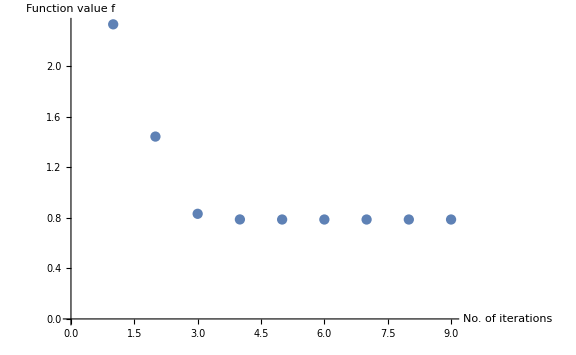

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

0.787262

#### Case 1.1.5: N=100, m=1/10, δ=1, dimS=1, l=4

```mathematica
CM0=partialCM[100,1/10,1,4,1,1];CM0//MatrixForm
```

(1.28101 | 0 | -0.0106767 | 0
0 | 1.39418 | 0 | 0.293694
-0.0106767 | 0 | 1.28101 | 0
0 | 0.293694 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,2,"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[8],"qpqp","qpqp"]
```

{{0.46489,0.305284},{{0.,0.658611,0.,0.658611},{-0.759173,0.,-0.759173,0.},{-0.679348,0.,0.679348,0.},{0.,-0.736,0.,0.736}}}

SparseArray[…]

{{0,-1,0,0,0,0,0,0},{1,0,0,0,0,0,0,0},{0,0,0,-1,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,0,0,-1,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,-1},{0,0,0,0,0,0,1,0}}

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4,"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(1+1),(1+1)},10^-9,∞];
```

Final value: 0.79114

Number of iterations: 9

Number of total corrections: 0

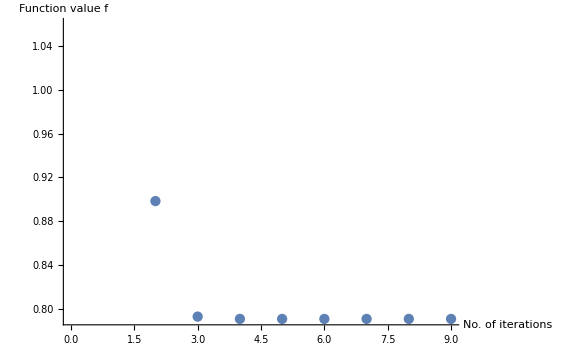

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

0.79114

#### Case 1.1.6: N=100, m=1/10, δ=1, dimS=1, l=5

```mathematica
CM0=partialCM[100,1/10,1,5,1,1];CM0//MatrixForm
```

(1.28101 | 0 | -0.00697557 | 0
0 | 1.39418 | 0 | 0.247118
-0.00697557 | 0 | 1.28101 | 0
0 | 0.247118 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,2,"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[8],"qpqp","qpqp"]
```

{{0.456261,0.322614},{{0.,-0.663717,0.,-0.663717},{0.753333,0.,0.753333,0.},{-0.686917,0.,0.686917,0.},{0.,-0.72789,0.,0.72789}}}

SparseArray[…]

{{0,-1,0,0,0,0,0,0},{1,0,0,0,0,0,0,0},{0,0,0,-1,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,0,0,-1,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,-1},{0,0,0,0,0,0,1,0}}

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4,"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(1+1),(1+1)},10^-9,∞];
```

Final value: 0.793601

Number of iterations: 10

Number of total corrections: 0

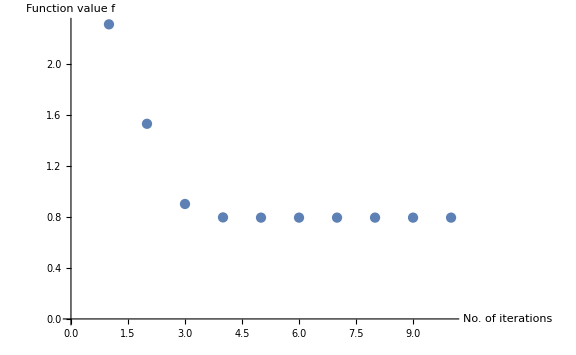

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

0.793601

#### Case 1.1.7: N=100, m=1/10, δ=1, dimS=1, l=10

```mathematica
CM0=partialCM[100,1/10,1,10,1,1];CM0//MatrixForm
```

(1.28101 | 0 | -0.0014811 | 0
0 | 1.39418 | 0 | 0.116311
-0.0014811 | 0 | 1.28101 | 0
0 | 0.116311 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,2,"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[8],"qpqp","qpqp"]
```

{{0.428481,0.366055},{{0.,0.678372,0.,0.678372},{-0.737059,0.,-0.737059,0.},{-0.706469,0.,0.706469,0.},{0.,-0.707745,0.,0.707745}}}

SparseArray[…]

{{0,-1,0,0,0,0,0,0},{1,0,0,0,0,0,0,0},{0,0,0,-1,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,0,0,-1,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,-1},{0,0,0,0,0,0,1,0}}

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4,"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(1+1),(1+1)},10^-9,∞];
```

Final value: 0.798164

Number of iterations: 9

Number of total corrections: 0

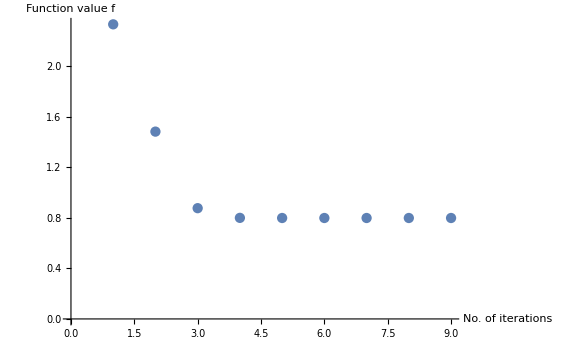

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

0.798164

#### Case 1.1.8: N=100, m=1/10, δ=1, dimS=1, l=15

```mathematica
CM0=partialCM[100,1/10,1,15,1,1];CM0//MatrixForm
```

(1.28101 | 0 | -0.000480174 | 0
0 | 1.39418 | 0 | 0.0598408
-0.000480174 | 0 | 1.28101 | 0
0 | 0.0598408 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,2,"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[8],"qpqp","qpqp"]
```

{{0.414912,0.382787},{{0.,0.684998,0.,0.684998},{-0.729929,0.,-0.729929,0.},{0.,-0.699998,0.,0.699998},{0.714288,0.,-0.714288,0.}}}

SparseArray[…]

{{0,-1,0,0,0,0,0,0},{1,0,0,0,0,0,0,0},{0,0,0,-1,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,0,0,-1,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,-1},{0,0,0,0,0,0,1,0}}

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4,"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(1+1),(1+1)},10^-9,∞];
```

Final value: 0.799105

Number of iterations: 8

Number of total corrections: 0

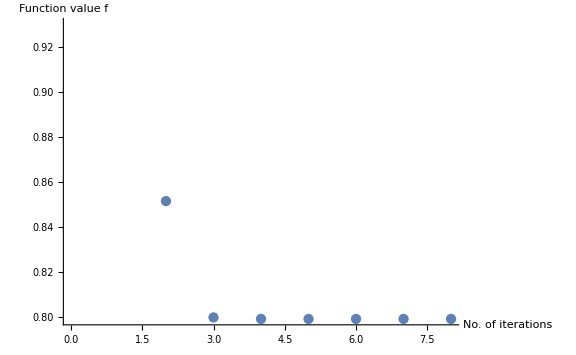

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

0.799105

#### Case 1.1.9: N=100, m=1/10, δ=1, dimS=1, l=20

```mathematica
CM0=partialCM[100,1/10,1,20,1,1];CM0//MatrixForm
```

(1.28101 | 0 | -0.00018661 | 0
0 | 1.39418 | 0 | 0.0321328
-0.00018661 | 0 | 1.28101 | 0
0 | 0.0321328 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,2,"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[8],"qpqp","qpqp"]
```

{{0.407887,0.390617},{{0.,0.68834,0.,0.68834},{-0.726385,0.,-0.726385,0.},{0.,-0.696371,0.,0.696371},{0.718008,0.,-0.718008,0.}}}

SparseArray[…]

{{0,-1,0,0,0,0,0,0},{1,0,0,0,0,0,0,0},{0,0,0,-1,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,0,0,-1,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,-1},{0,0,0,0,0,0,1,0}}

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4,"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(1+1),(1+1)},10^-9,∞];
```

Final value: 0.799346

Number of iterations: 8

Number of total corrections: 0

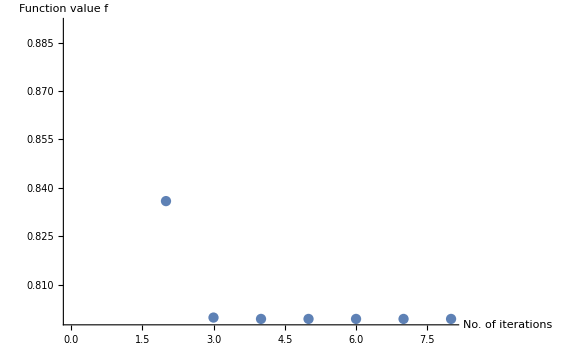

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

0.799346

#### Case 1.1.10: N=100, m=1/10, δ=1, dimS=1, l=30

```mathematica
CM0=partialCM[100,1/10,1,30,1,1];CM0//MatrixForm
```

(1.28101 | 0 | -0.0000369176 | 0
0 | 1.39418 | 0 | 0.0100091
-0.0000369176 | 0 | 1.28101 | 0
0 | 0.0100091 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,2,"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[8],"qpqp","qpqp"]
```

{{0.402094,0.396705},{{0.,-0.691056,0.,-0.691056},{0.72353,0.,0.72353,0.},{0.,-0.693551,0.,0.693551},{0.720927,0.,-0.720927,0.}}}

SparseArray[…]

{{0,-1,0,0,0,0,0,0},{1,0,0,0,0,0,0,0},{0,0,0,-1,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,0,0,-1,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,-1},{0,0,0,0,0,0,1,0}}

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4,"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(1+1),(1+1)},10^-9,∞];
```

Final value: 0.799434

Number of iterations: 10

Number of total corrections: 0

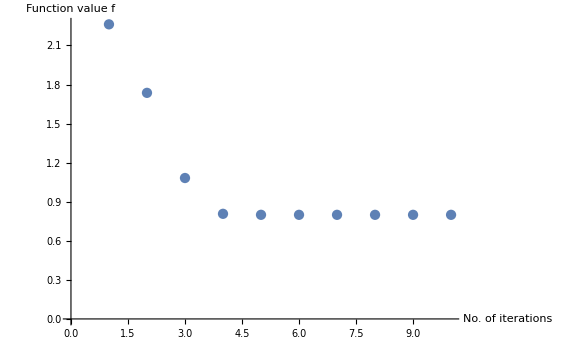

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

0.799434

#### Case 1.1.11: N=100, m=1/10, δ=1, dimS=1, l=45

```mathematica
CM0=partialCM[100,1/10,1,45,1,1];CM0//MatrixForm
```

(1.28101 | 0 | -5.9252×10^-6 | 0
0 | 1.39418 | 0 | 0.00258647
-5.9252×10^-6 | 0 | 1.28101 | 0
0 | 0.00258647 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,2,"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[8],"qpqp","qpqp"]
```

{{0.400112,0.398717},{{0.,-0.691976,0.,-0.691976},{0.722568,0.,0.722568,0.},{0.,-0.69262,0.,0.69262},{0.721896,0.,-0.721896,0.}}}

SparseArray[…]

{{0,-1,0,0,0,0,0,0},{1,0,0,0,0,0,0,0},{0,0,0,-1,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,0,0,-1,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,-1},{0,0,0,0,0,0,1,0}}

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4,"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(1+1),(1+1)},10^-9,∞];
```

Final value: 0.799442

Number of iterations: 9

Number of total corrections: 0

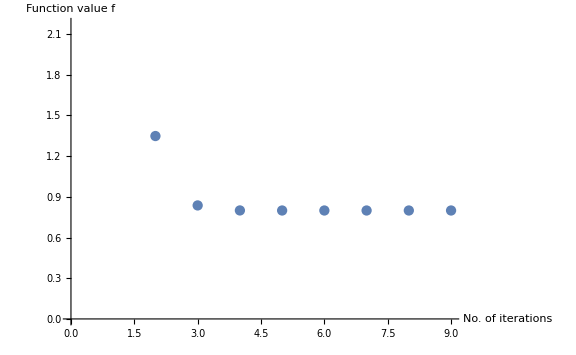

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

0.799442

#### Case 1.1.12: N=100, m=1/10, δ=1, dimS=1, l=46

```mathematica
CM0=partialCM[100,1/10,1,46,1,1];CM0//MatrixForm
```

(1.28101 | 0 | -5.58759×10^-6 | 0
0 | 1.39418 | 0 | 0.00248335
-5.58759×10^-6 | 0 | 1.28101 | 0
0 | 0.00248335 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,2,"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[8],"qpqp","qpqp"]
```

{{0.400084,0.398745},{{0.,0.691989,0.,0.691989},{-0.722555,0.,-0.722555,0.},{0.,-0.692607,0.,0.692607},{0.72191,0.,-0.72191,0.}}}

SparseArray[…]

{{0,-1,0,0,0,0,0,0},{1,0,0,0,0,0,0,0},{0,0,0,-1,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,0,0,-1,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,-1},{0,0,0,0,0,0,1,0}}

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4,"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(1+1),(1+1)},10^-9,∞];
```

Final value: 0.799442

Number of iterations: 9

Number of total corrections: 1

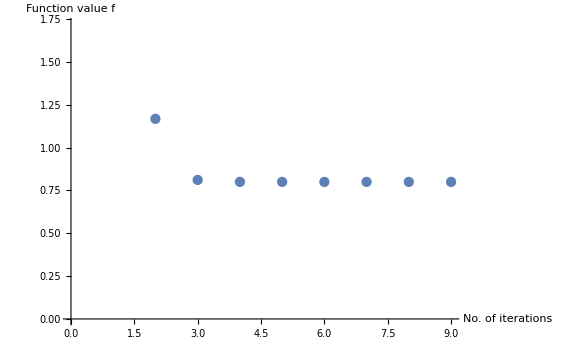

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

0.799442

#### Case 1.1.13: N=100, m=1/10, δ=1, dimS=1, l=47

```mathematica
CM0=partialCM[100,1/10,1,47,1,1];CM0//MatrixForm
```

(1.28101 | 0 | -5.35149×10^-6 | 0
0 | 1.39418 | 0 | 0.00241066
-5.35149×10^-6 | 0 | 1.28101 | 0
0 | 0.00241066 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,2,"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[8],"qpqp","qpqp"]
```

{{0.400064,0.398764},{{0.,0.691998,0.,0.691998},{-0.722545,0.,-0.722545,0.},{0.,-0.692598,0.,0.692598},{0.721919,0.,-0.721919,0.}}}

SparseArray[…]

{{0,-1,0,0,0,0,0,0},{1,0,0,0,0,0,0,0},{0,0,0,-1,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,0,0,-1,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,-1},{0,0,0,0,0,0,1,0}}

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4,"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(1+1),(1+1)},10^-9,∞];
```

Final value: 0.799442

Number of iterations: 7

Number of total corrections: 0

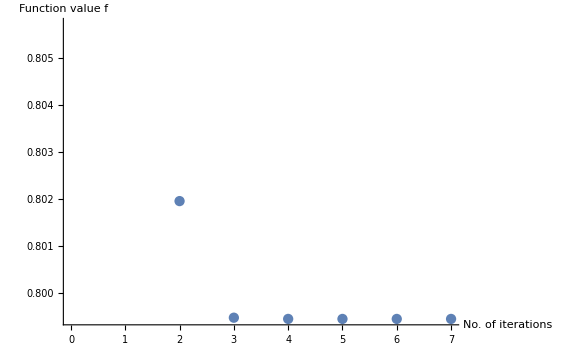

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

0.799442

#### Case 1.1.14: N=100, m=1/10, δ=1, dimS=1, l=48

```mathematica
CM0=partialCM[100,1/10,1,48,1,1];CM0//MatrixForm
```

(1.28101 | 0 | -5.21181×10^-6 | 0
0 | 1.39418 | 0 | 0.00236743
-5.21181×10^-6 | 0 | 1.28101 | 0
0 | 0.00236743 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,2,"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[8],"qpqp","qpqp"]
```

{{0.400053,0.398776},{{0.,0.692004,0.,0.692004},{-0.722539,0.,-0.722539,0.},{0.,-0.692593,0.,0.692593},{0.721925,0.,-0.721925,0.}}}

SparseArray[…]

{{0,-1,0,0,0,0,0,0},{1,0,0,0,0,0,0,0},{0,0,0,-1,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,0,0,-1,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,-1},{0,0,0,0,0,0,1,0}}

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4,"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(1+1),(1+1)},10^-9,∞];
```

Final value: 0.799443

Number of iterations: 9

Number of total corrections: 1

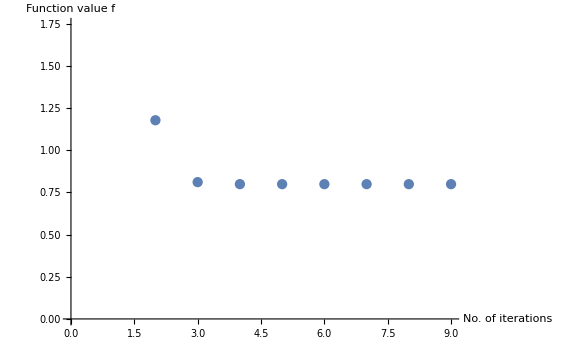

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

0.799443

#### Case 1.1.15: N=100, m=1/10, δ=1, dimS=1, l=49

```mathematica
CM0=partialCM[100,1/10,1,49,1,1];CM0//MatrixForm
```

(1.28101 | 0 | -5.16558×10^-6 | 0
0 | 1.39418 | 0 | 0.00235308
-5.16558×10^-6 | 0 | 1.28101 | 0
0 | 0.00235308 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,2,"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[8],"qpqp","qpqp"]
```

{{0.400049,0.39878},{{0.,0.692006,0.,0.692006},{-0.722538,0.,-0.722538,0.},{0.,-0.692591,0.,0.692591},{0.721927,0.,-0.721927,0.}}}

SparseArray[…]

{{0,-1,0,0,0,0,0,0},{1,0,0,0,0,0,0,0},{0,0,0,-1,0,0,0,0},{0,0,1,0,0,0,0,0},{0,0,0,0,0,-1,0,0},{0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,-1},{0,0,0,0,0,0,1,0}}

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4,"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(1+1),(1+1)},10^-9,∞];
```

Final value: 0.799443

Number of iterations: 8

Number of total corrections: 0

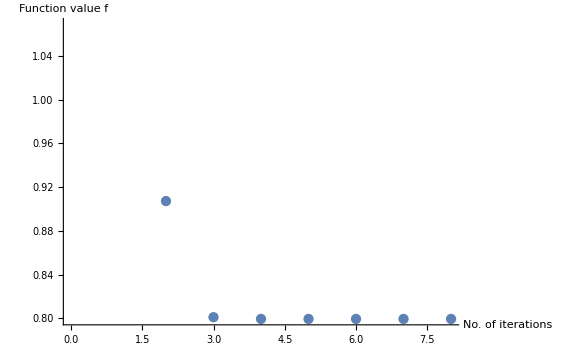

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

0.799443

#### Summary Case 1.1

```mathematica
listCase11={{0,0.7074591735168936},{1,0.7672233438804287},{2,0.7806345878621787},{3,0.7872619247999597},{4,0.7911400250356868},{5,0.7936011522537301},{10,0.7981635927445374},{15,0.7991053475076283},{20,0.7993457814692719},{30,0.7994336154396451},{45,0.799442414994183},{46,0.7994424641780215},{47,0.7994424976489363},{48,0.799442517083822},{49,0.7994425234562166}};
```

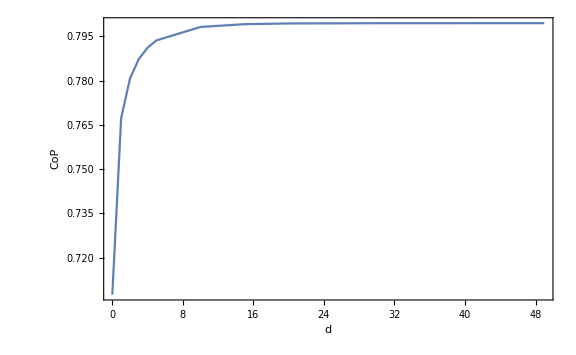

```mathematica
ListPlot[listCase11,PlotRange->All, Joined->True,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50]
```

In this case, Complexity of Purification (CoP) seems to be monotonically increasing with the distance between the subsystems. There is no plateau-like structure for small separation. It can also be seen that for a separation of order 10^1, CoP saturates.

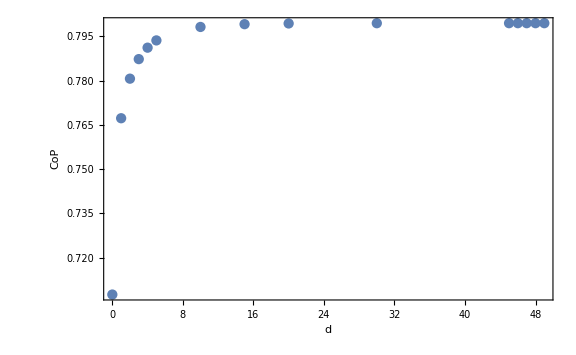
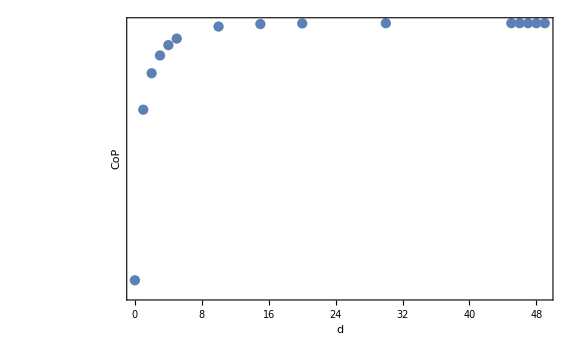

```mathematica
PlotlistCase11=Row[{ListPlot[listCase11,PlotRange->All,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50],ListLogPlot[listCase11,PlotRange->All,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50]}]
Export[NotebookDirectory[]<>"PlotlistCase11.pdf",PlotlistCase11];
```

### Case 1.2: N=100, m=1/10, δ=1, dimS=2

#### Case 1.2.1: N=100, m=1/10, δ=1, dimS=2, l=0

```mathematica
CM0=partialCM[100,1/10,1,0,2,2];CM0//MatrixForm
```

(1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0
0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315
-0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0
0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542
-0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0
0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649
-0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0
0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,(2+2),"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[4(2+2)],"qpqp","qpqp"];
```

{{0.406088,0.215895,0.0215537,0.00399736},{{0.,-0.473851,0.,-0.164523,0.,-0.164523,0.,-0.473851},{0.803418,0.,0.725127,0.,0.725127,0.,0.803418,0.},{-0.65825,0.,-0.195085,0.,0.195085,0.,0.65825,0.},{0.,-0.73008,0.,-0.0995702,0.,0.0995702,0.,0.73008},{0.210653,0.,-0.606712,0.,-0.606712,0.,0.210653,0.},{0.,0.566334,0.,-0.62748,0.,-0.62748,0.,0.566334},{0.0715321,0.,-0.524496,0.,0.524496,0.,-0.0715321,0.},{0.,0.271552,0.,-0.916261,0.,0.916261,0.,-0.271552}}}

SparseArray[…]

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4(2),"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(2+2),(2+2)},10^-9,∞];
```

Final value: 0.890738

Number of iterations: 10

Number of total corrections: 0

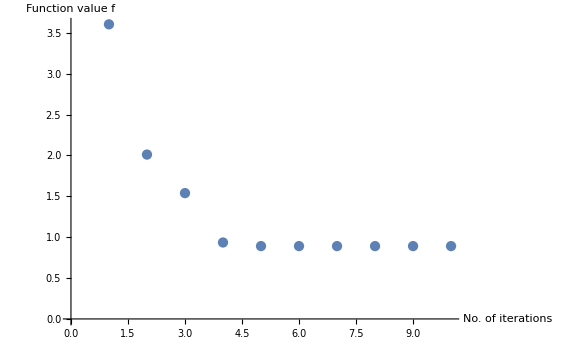

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

0.890738

#### Case 1.2.2: N=100, m=1/10, δ=1, dimS=2, l=1

```mathematica
CM0=partialCM[100,1/10,1,1,2,2];CM0//MatrixForm
```

(1.28101 | 0 | -0.41982 | 0 | -0.0334432 | 0 | -0.0177027 | 0
0 | 1.39418 | 0 | 0.760649 | 0 | 0.435315 | 0 | 0.353884
-0.41982 | 0 | 1.28101 | 0 | -0.0813337 | 0 | -0.0334432 | 0
0 | 0.760649 | 0 | 1.39418 | 0 | 0.554542 | 0 | 0.435315
-0.0334432 | 0 | -0.0813337 | 0 | 1.28101 | 0 | -0.41982 | 0
0 | 0.435315 | 0 | 0.554542 | 0 | 1.39418 | 0 | 0.760649
-0.0177027 | 0 | -0.0334432 | 0 | -0.41982 | 0 | 1.28101 | 0
0 | 0.353884 | 0 | 0.435315 | 0 | 0.760649 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,(2+2),"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[4(2+2)],"qpqp","qpqp"];
```

{{0.498362,0.237597,0.150009,0.00695197},{{0.,0.334637,0.,0.374853,0.,0.374853,0.,0.334637},{-0.671292,0.,-0.734583,0.,-0.734583,0.,-0.671292,0.},{-0.67583,0.,-0.294457,0.,0.294457,0.,0.67583,0.},{0.,-0.685117,0.,-0.125579,0.,0.125579,0.,0.685117},{-0.415423,0.,0.370854,0.,0.370854,0.,-0.415423,0.},{0.,-0.662845,0.,0.605734,0.,0.605734,0.,-0.662845},{0.10419,0.,-0.568427,0.,0.568427,0.,-0.10419,0.},{0.,0.354905,0.,-0.814569,0.,0.814569,0.,-0.354905}}}

SparseArray[…]

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4(2),"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(2+2),(2+2)},10^-9,∞];
```

Final value: 0.956594

Number of iterations: 9

Number of total corrections: 0

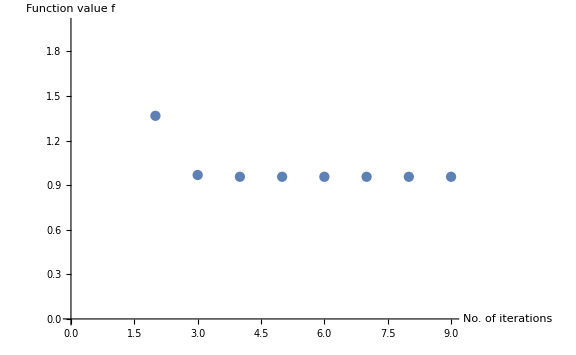

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

0.956594

#### Case 1.2.3: N=100, m=1/10, δ=1, dimS=2, l=2

```mathematica
CM0=partialCM[100,1/10,1,2,2,2];CM0//MatrixForm
```

(1.28101 | 0 | -0.41982 | 0 | -0.0177027 | 0 | -0.0106767 | 0
0 | 1.39418 | 0 | 0.760649 | 0 | 0.353884 | 0 | 0.293694
-0.41982 | 0 | 1.28101 | 0 | -0.0334432 | 0 | -0.0177027 | 0
0 | 0.760649 | 0 | 1.39418 | 0 | 0.435315 | 0 | 0.353884
-0.0177027 | 0 | -0.0334432 | 0 | 1.28101 | 0 | -0.41982 | 0
0 | 0.353884 | 0 | 0.435315 | 0 | 1.39418 | 0 | 0.760649
-0.0106767 | 0 | -0.0177027 | 0 | -0.41982 | 0 | 1.28101 | 0
0 | 0.293694 | 0 | 0.353884 | 0 | 0.760649 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,(2+2),"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[4(2+2)],"qpqp","qpqp"];
```

{{0.497468,0.26826,0.146622,0.0970826},{{0.,-0.339803,0.,-0.390006,0.,-0.390006,0.,-0.339803},{0.655902,0.,0.71056,0.,0.71056,0.,0.655902,0.},{0.,0.596893,0.,0.250308,0.,-0.250308,0.,-0.596893},{-0.661218,0.,-0.420779,0.,0.420779,0.,0.661218,0.},{0.418406,0.,-0.364547,0.,-0.364547,0.,0.418406,0.},{0.,0.66233,0.,-0.611382,0.,-0.611382,0.,0.66233},{-0.218365,0.,0.520722,0.,-0.520722,0.,0.218365,0.},{0.,-0.48233,0.,0.75794,0.,-0.75794,0.,0.48233}}}

SparseArray[…]

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4(2),"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(2+2),(2+2)},10^-9,∞];
```

Final value: 0.973802

Number of iterations: 10

Number of total corrections: 0

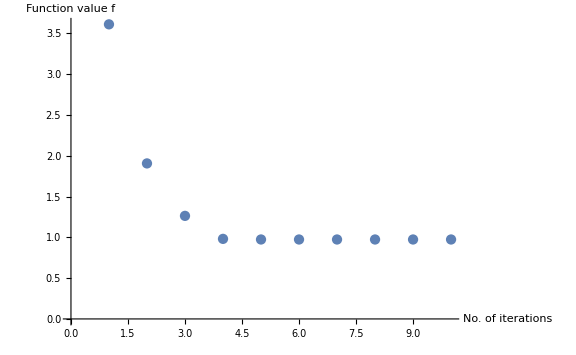

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

0.973802

#### Case 1.2.4: N=100, m=1/10, δ=1, dimS=2, l=3

```mathematica
CM0=partialCM[100,1/10,1,3,2,2];CM0//MatrixForm
```

(1.28101 | 0 | -0.41982 | 0 | -0.0106767 | 0 | -0.00697557 | 0
0 | 1.39418 | 0 | 0.760649 | 0 | 0.293694 | 0 | 0.247118
-0.41982 | 0 | 1.28101 | 0 | -0.0177027 | 0 | -0.0106767 | 0
0 | 0.760649 | 0 | 1.39418 | 0 | 0.353884 | 0 | 0.293694
-0.0106767 | 0 | -0.0177027 | 0 | 1.28101 | 0 | -0.41982 | 0
0 | 0.293694 | 0 | 0.353884 | 0 | 1.39418 | 0 | 0.760649
-0.00697557 | 0 | -0.0106767 | 0 | -0.41982 | 0 | 1.28101 | 0
0 | 0.247118 | 0 | 0.293694 | 0 | 0.760649 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,(2+2),"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[4(2+2)],"qpqp","qpqp"];
```

{{0.489482,0.295129,0.143934,0.116778},{{0.,-0.347893,0.,-0.394144,0.,-0.394144,0.,-0.347893},{0.649608,0.,0.695193,0.,0.695193,0.,0.649608,0.},{0.,-0.533833,0.,-0.317167,0.,0.317167,0.,0.533833},{0.644815,0.,0.491151,0.,-0.491151,0.,-0.644815,0.},{-0.415419,0.,0.366671,0.,0.366671,0.,-0.415419,0.},{0.,-0.659589,0.,0.61634,0.,0.61634,0.,-0.659589},{0.28455,0.,-0.478935,0.,0.478935,0.,-0.28455,0.},{0.,0.547449,0.,-0.718727,0.,0.718727,0.,-0.547449}}}

SparseArray[…]

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4(2),"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(2+2),(2+2)},10^-9,∞];
```

Final value: 0.982673

Number of iterations: 9

Number of total corrections: 1

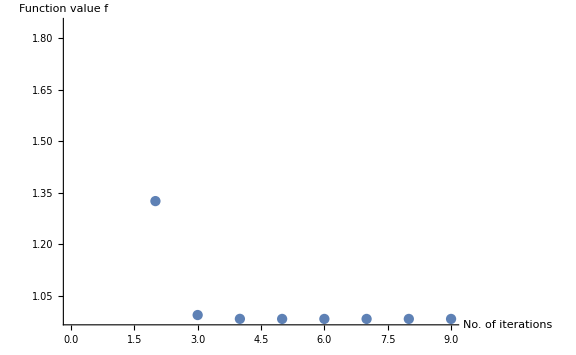

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

0.982673

#### Case 1.2.5: N=100, m=1/10, δ=1, dimS=2, l=4

```mathematica
CM0=partialCM[100,1/10,1,4,2,2];CM0//MatrixForm
```

(1.28101 | 0 | -0.41982 | 0 | -0.00697557 | 0 | -0.0048107 | 0
0 | 1.39418 | 0 | 0.760649 | 0 | 0.247118 | 0 | 0.209989
-0.41982 | 0 | 1.28101 | 0 | -0.0106767 | 0 | -0.00697557 | 0
0 | 0.760649 | 0 | 1.39418 | 0 | 0.293694 | 0 | 0.247118
-0.00697557 | 0 | -0.0106767 | 0 | 1.28101 | 0 | -0.41982 | 0
0 | 0.247118 | 0 | 0.293694 | 0 | 1.39418 | 0 | 0.760649
-0.0048107 | 0 | -0.00697557 | 0 | -0.41982 | 0 | 1.28101 | 0
0 | 0.209989 | 0 | 0.247118 | 0 | 0.760649 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,(2+2),"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[4(2+2)],"qpqp","qpqp"];
```

{{0.480922,0.316223,0.142229,0.125062},{{0.,0.35492,0.,0.395822,0.,0.395822,0.,0.35492},{-0.645779,0.,-0.684146,0.,-0.684146,0.,-0.645779,0.},{0.,0.495248,0.,0.350071,0.,-0.350071,0.,-0.495248},{-0.634962,0.,-0.529997,0.,0.529997,0.,0.634962,0.},{-0.412178,0.,0.369586,0.,0.369586,0.,-0.412178,0.},{0.,-0.656998,0.,0.620153,0.,0.620153,0.,-0.656998},{0.319912,0.,-0.452583,0.,0.452583,0.,-0.319912,0.},{0.,0.579959,0.,-0.69482,0.,0.69482,0.,-0.579959}}}

SparseArray[…]

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4(2),"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(2+2),(2+2)},10^-9,∞];
```

Final value: 0.987995

Number of iterations: 9

Number of total corrections: 0

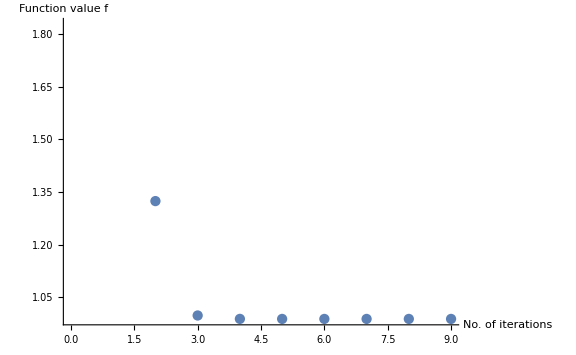

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

0.987995

#### Case 1.2.6: N=100, m=1/10, δ=1, dimS=2, l=5

```mathematica
CM0=partialCM[100,1/10,1,5,2,2];CM0//MatrixForm
```

(1.28101 | 0 | -0.41982 | 0 | -0.0048107 | 0 | -0.00344953 | 0
0 | 1.39418 | 0 | 0.760649 | 0 | 0.209989 | 0 | 0.179771
-0.41982 | 0 | 1.28101 | 0 | -0.00697557 | 0 | -0.0048107 | 0
0 | 0.760649 | 0 | 1.39418 | 0 | 0.247118 | 0 | 0.209989
-0.0048107 | 0 | -0.00697557 | 0 | 1.28101 | 0 | -0.41982 | 0
0 | 0.209989 | 0 | 0.247118 | 0 | 1.39418 | 0 | 0.760649
-0.00344953 | 0 | -0.0048107 | 0 | -0.41982 | 0 | 1.28101 | 0
0 | 0.179771 | 0 | 0.209989 | 0 | 0.760649 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,(2+2),"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[4(2+2)],"qpqp","qpqp"];
```

{{0.472988,0.332629,0.141112,0.129291},{{0.,0.360775,0.,0.396659,0.,0.396659,0.,0.360775},{-0.643032,0.,-0.67567,0.,-0.67567,0.,-0.643032,0.},{0.,0.470868,0.,0.367524,0.,-0.367524,0.,-0.470868},{-0.62966,0.,-0.553741,0.,0.553741,0.,0.62966,0.},{0.409321,0.,-0.372291,0.,-0.372291,0.,0.409321,0.},{0.,0.654768,0.,-0.62314,0.,-0.62314,0.,0.654768},{0.340329,0.,-0.436026,0.,0.436026,0.,-0.340329,0.},{0.,0.59799,0.,-0.679974,0.,0.679974,0.,-0.59799}}}

SparseArray[…]

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4(2),"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(2+2),(2+2)},10^-9,∞];
```

Final value: 0.991432

Number of iterations: 10

Number of total corrections: 0

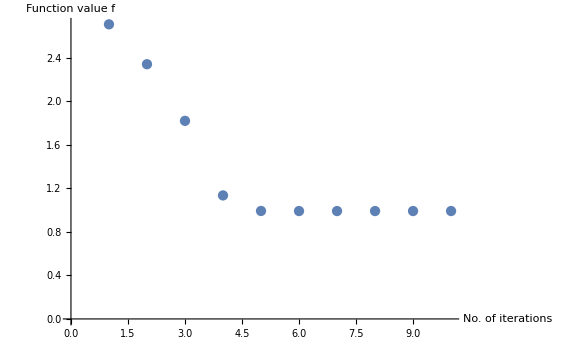

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

0.991432

#### Case 1.2.7: N=100, m=1/10, δ=1, dimS=2, l=8

```mathematica
CM0=partialCM[100,1/10,1,8,2,2];CM0//MatrixForm
```

(1.28101 | 0 | -0.41982 | 0 | -0.00192459 | 0 | -0.0014811 | 0
0 | 1.39418 | 0 | 0.760649 | 0 | 0.133923 | 0 | 0.116311
-0.41982 | 0 | 1.28101 | 0 | -0.00254724 | 0 | -0.00192459 | 0
0 | 0.760649 | 0 | 1.39418 | 0 | 0.154799 | 0 | 0.133923
-0.00192459 | 0 | -0.00254724 | 0 | 1.28101 | 0 | -0.41982 | 0
0 | 0.133923 | 0 | 0.154799 | 0 | 1.39418 | 0 | 0.760649
-0.0014811 | 0 | -0.00192459 | 0 | -0.41982 | 0 | 1.28101 | 0
0 | 0.116311 | 0 | 0.133923 | 0 | 0.760649 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,(2+2),"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[4(2+2)],"qpqp","qpqp"];
```

{{0.454211,0.36437,0.139371,0.134277},{{0.,0.373308,0.,0.397579,0.,0.397579,0.,0.373308},{-0.637782,0.,-0.658764,0.,-0.658764,0.,-0.637782,0.},{0.,0.434527,0.,0.387706,0.,-0.387706,0.,-0.434527},{-0.624861,0.,-0.589315,0.,0.589315,0.,0.624861,0.},{0.403023,0.,-0.37842,0.,-0.37842,0.,0.403023,0.},{0.,0.649865,0.,-0.629167,0.,-0.629167,0.,0.649865},{0.367738,0.,-0.412147,0.,0.412147,0.,-0.367738,0.},{0.,0.621315,0.,-0.65879,0.,0.65879,0.,-0.621315}}}

SparseArray[…]

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4(2),"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(2+2),(2+2)},10^-9,∞];
```

Final value: 0.996523

Number of iterations: 9

Number of total corrections: 0

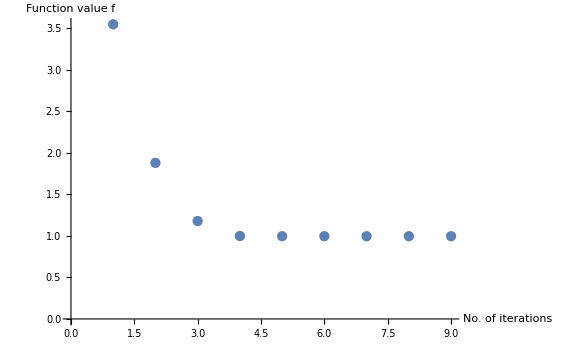

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

0.996523

#### Case 1.2.8: N=100, m=1/10, δ=1, dimS=2, l=10

```mathematica
CM0=partialCM[100,1/10,1,10,2,2];CM0//MatrixForm
```

(1.28101 | 0 | -0.41982 | 0 | -0.00115709 | 0 | -0.000915362 | 0
0 | 1.39418 | 0 | 0.760649 | 0 | 0.101343 | 0 | 0.0885453
-0.41982 | 0 | 1.28101 | 0 | -0.0014811 | 0 | -0.00115709 | 0
0 | 0.760649 | 0 | 1.39418 | 0 | 0.116311 | 0 | 0.101343
-0.00115709 | 0 | -0.0014811 | 0 | 1.28101 | 0 | -0.41982 | 0
0 | 0.101343 | 0 | 0.116311 | 0 | 1.39418 | 0 | 0.760649
-0.000915362 | 0 | -0.00115709 | 0 | -0.41982 | 0 | 1.28101 | 0
0 | 0.0885453 | 0 | 0.101343 | 0 | 0.760649 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,(2+2),"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[4(2+2)],"qpqp","qpqp"];
```

{{0.445226,0.377118,0.1388,0.135503},{{0.,-0.378918,0.,-0.397744,0.,-0.397744,0.,-0.378918},{0.635602,0.,0.651571,0.,0.651571,0.,0.635602,0.},{0.,0.423069,0.,0.392225,0.,-0.392225,0.,-0.423069},{-0.624699,0.,-0.600954,0.,0.600954,0.,0.624699,0.},{0.400168,0.,-0.381227,0.,-0.381227,0.,0.400168,0.},{0.,0.647625,0.,-0.631753,0.,-0.631753,0.,0.647625},{-0.375494,0.,0.405023,0.,-0.405023,0.,0.375494,0.},{0.,-0.62773,0.,0.652533,0.,-0.652533,0.,0.62773}}}

SparseArray[…]

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4(2),"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(2+2),(2+2)},10^-9,∞];
```

Final value: 0.99797

Number of iterations: 7

Number of total corrections: 0

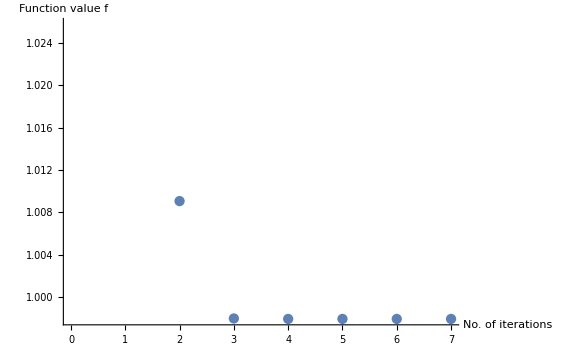

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

0.99797

#### Case 1.2.9: N=100, m=1/10, δ=1, dimS=2, l=15

```mathematica
CM0=partialCM[100,1/10,1,15,2,2];CM0//MatrixForm
```

(1.28101 | 0 | -0.41982 | 0 | -0.000393171 | 0 | -0.00032389 | 0
0 | 1.39418 | 0 | 0.760649 | 0 | 0.0527011 | 0 | 0.0464815
-0.41982 | 0 | 1.28101 | 0 | -0.000480174 | 0 | -0.000393171 | 0
0 | 0.760649 | 0 | 1.39418 | 0 | 0.0598408 | 0 | 0.0527011
-0.000393171 | 0 | -0.000480174 | 0 | 1.28101 | 0 | -0.41982 | 0
0 | 0.0527011 | 0 | 0.0598408 | 0 | 1.39418 | 0 | 0.760649
-0.00032389 | 0 | -0.000393171 | 0 | -0.41982 | 0 | 1.28101 | 0
0 | 0.0464815 | 0 | 0.0527011 | 0 | 0.760649 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,(2+2),"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[4(2+2)],"qpqp","qpqp"];
```

{{0.430786,0.395223,0.138089,0.136727},{{0.,-0.387634,0.,-0.397767,0.,-0.397767,0.,-0.387634},{0.63238,0.,0.640748,0.,0.640748,0.,0.63238,0.},{0.,-0.409189,0.,-0.396107,0.,0.396107,0.,0.409189},{0.625945,0.,0.615666,0.,-0.615666,0.,-0.625945,0.},{0.395702,0.,-0.385621,0.,-0.385621,0.,0.395702,0.},{0.,0.644092,0.,-0.63568,0.,-0.63568,0.,0.644092},{0.384164,0.,-0.396851,0.,0.396851,0.,-0.384164,0.},{0.,0.634808,0.,-0.645406,0.,0.645406,0.,-0.634808}}}

SparseArray[…]

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4(2),"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(2+2),(2+2)},10^-9,∞];
```

Final value: 0.999362

Number of iterations: 9

Number of total corrections: 0

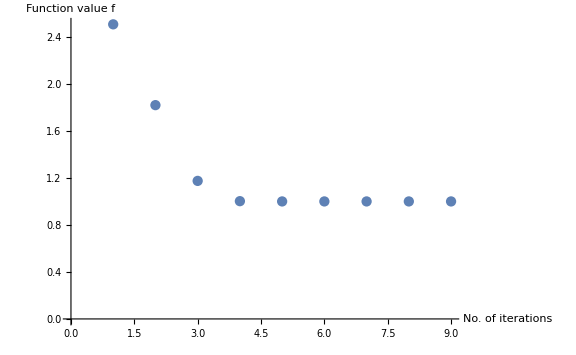

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

0.999362

#### Case 1.2.10: N=100, m=1/10, δ=1, dimS=2, l=20

```mathematica
CM0=partialCM[100,1/10,1,20,2,2];CM0//MatrixForm
```

(1.28101 | 0 | -0.41982 | 0 | -0.000156594 | 0 | -0.000131877 | 0
0 | 1.39418 | 0 | 0.760649 | 0 | 0.0284749 | 0 | 0.0252583
-0.41982 | 0 | 1.28101 | 0 | -0.00018661 | 0 | -0.000156594 | 0
0 | 0.760649 | 0 | 1.39418 | 0 | 0.0321328 | 0 | 0.0284749
-0.000156594 | 0 | -0.00018661 | 0 | 1.28101 | 0 | -0.41982 | 0
0 | 0.0284749 | 0 | 0.0321328 | 0 | 1.39418 | 0 | 0.760649
-0.000131877 | 0 | -0.000156594 | 0 | -0.41982 | 0 | 1.28101 | 0
0 | 0.0252583 | 0 | 0.0284749 | 0 | 0.760649 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,(2+2),"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[4(2+2)],"qpqp","qpqp"];
```

{{0.423124,0.403847,0.137787,0.137138},{{0.,-0.392148,0.,-0.397678,0.,-0.397678,0.,-0.392148},{0.630781,0.,0.635288,0.,0.635288,0.,0.630781,0.},{0.,-0.403434,0.,-0.397086,0.,0.397086,0.,0.403434},{0.627093,0.,0.622055,0.,-0.622055,0.,-0.627093,0.},{0.393376,0.,-0.387906,0.,-0.387906,0.,0.393376,0.},{0.,0.642236,0.,-0.63768,0.,-0.63768,0.,0.642236},{0.387474,0.,-0.393668,0.,0.393668,0.,-0.387474,0.},{0.,0.637487,0.,-0.642649,0.,0.642649,0.,-0.637487}}}

SparseArray[…]

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4(2),"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(2+2),(2+2)},10^-9,∞];
```

Final value: 0.999723

Number of iterations: 9

Number of total corrections: 0

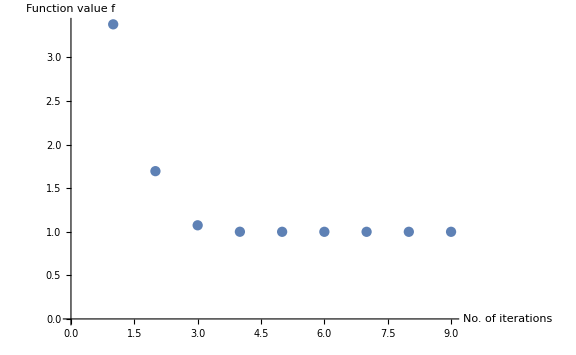

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

0.999723

#### Case 1.2.11: N=100, m=1/10, δ=1, dimS=2, l=30

```mathematica
CM0=partialCM[100,1/10,1,30,2,2];CM0//MatrixForm
```

(1.28101 | 0 | -0.41982 | 0 | -0.000031822 | 0 | -0.000027491 | 0
0 | 1.39418 | 0 | 0.760649 | 0 | 0.00895661 | 0 | 0.00802546
-0.41982 | 0 | 1.28101 | 0 | -0.0000369176 | 0 | -0.000031822 | 0
0 | 0.760649 | 0 | 1.39418 | 0 | 0.0100091 | 0 | 0.00895661
-0.000031822 | 0 | -0.0000369176 | 0 | 1.28101 | 0 | -0.41982 | 0
0 | 0.00895661 | 0 | 0.0100091 | 0 | 1.39418 | 0 | 0.760649
-0.000027491 | 0 | -0.000031822 | 0 | -0.41982 | 0 | 1.28101 | 0
0 | 0.00802546 | 0 | 0.00895661 | 0 | 0.760649 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,(2+2),"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[4(2+2)],"qpqp","qpqp"];
```

{{0.416709,0.410621,0.13757,0.137392},{{0.,0.395878,0.,0.397555,0.,0.397555,0.,0.395878},{-0.629495,0.,-0.630847,0.,-0.630847,0.,-0.629495,0.},{0.,-0.399265,0.,-0.397514,0.,0.397514,0.,0.399265},{0.628225,0.,0.626825,0.,-0.626825,0.,-0.628225,0.},{-0.391448,0.,0.389797,0.,0.389797,0.,-0.391448,0.},{0.,-0.64069,0.,0.639317,0.,0.639317,0.,-0.64069},{0.389745,0.,-0.391462,0.,0.391462,0.,-0.389745,0.},{0.,0.63932,0.,-0.640748,0.,0.640748,0.,-0.63932}}}

SparseArray[…]

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4(2),"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(2+2),(2+2)},10^-9,∞];
```

Final value: 0.999857

Number of iterations: 10

Number of total corrections: 0

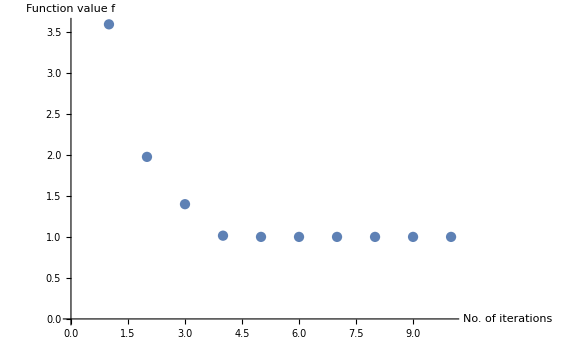

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

0.999857

#### Case 1.2.12: N=100, m=1/10, δ=1, dimS=2, l=40

```mathematica
CM0=partialCM[100,1/10,1,40,2,2];CM0//MatrixForm
```

(1.28101 | 0 | -0.41982 | 0 | -8.47426×10^-6 | 0 | -7.6322×10^-6 | 0
0 | 1.39418 | 0 | 0.760649 | 0 | 0.00333708 | 0 | 0.00309418
-0.41982 | 0 | 1.28101 | 0 | -9.48153×10^-6 | 0 | -8.47426×10^-6 | 0
0 | 0.760649 | 0 | 1.39418 | 0 | 0.00362182 | 0 | 0.00333708
-8.47426×10^-6 | 0 | -9.48153×10^-6 | 0 | 1.28101 | 0 | -0.41982 | 0
0 | 0.00333708 | 0 | 0.00362182 | 0 | 1.39418 | 0 | 0.760649
-7.6322×10^-6 | 0 | -8.47426×10^-6 | 0 | -0.41982 | 0 | 1.28101 | 0
0 | 0.00309418 | 0 | 0.00333708 | 0 | 0.760649 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,(2+2),"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[4(2+2)],"qpqp","qpqp"];
```

{{0.414819,0.412545,0.137513,0.137452},{{0.,-0.397013,0.,-0.397466,0.,-0.397466,0.,-0.397013},{0.629162,0.,0.629525,0.,0.629525,0.,0.629162,0.},{0.,-0.398091,0.,-0.397631,0.,0.397631,0.,0.398091},{0.628545,0.,0.628176,0.,-0.628176,0.,-0.628545,0.},{0.390839,0.,-0.390394,0.,-0.390394,0.,0.390839,0.},{0.,0.640199,0.,-0.639829,0.,-0.639829,0.,0.640199},{-0.390384,0.,0.390836,0.,-0.390836,0.,0.390384,0.},{0.,-0.639836,0.,0.640212,0.,-0.640212,0.,0.639836}}}

SparseArray[…]

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4(2),"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(2+2),(2+2)},10^-9,∞];
```

Final value: 0.999869

Number of iterations: 8

Number of total corrections: 0

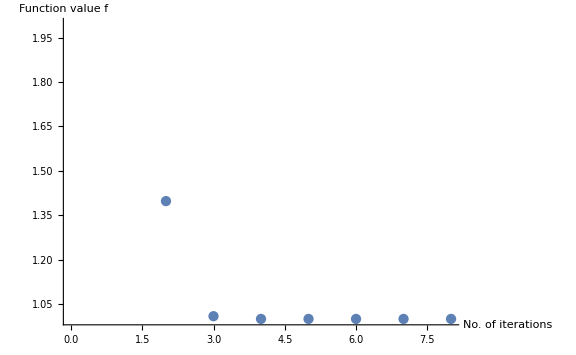

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

0.999869

#### Case 1.2.13: N=100, m=1/10, δ=1, dimS=2, l=45

```mathematica
CM0=partialCM[100,1/10,1,45,2,2];CM0//MatrixForm
```

(1.28101 | 0 | -0.41982 | 0 | -5.58759×10^-6 | 0 | -5.35149×10^-6 | 0
0 | 1.39418 | 0 | 0.760649 | 0 | 0.00248335 | 0 | 0.00241066
-0.41982 | 0 | 1.28101 | 0 | -5.9252×10^-6 | 0 | -5.58759×10^-6 | 0
0 | 0.760649 | 0 | 1.39418 | 0 | 0.00258647 | 0 | 0.00248335
-5.58759×10^-6 | 0 | -5.9252×10^-6 | 0 | 1.28101 | 0 | -0.41982 | 0
0 | 0.00248335 | 0 | 0.00258647 | 0 | 1.39418 | 0 | 0.760649
-5.35149×10^-6 | 0 | -5.58759×10^-6 | 0 | -0.41982 | 0 | 1.28101 | 0
0 | 0.00241066 | 0 | 0.00248335 | 0 | 0.760649 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,(2+2),"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[4(2+2)],"qpqp","qpqp"];
```

{{0.41453,0.412837,0.137505,0.13746},{{0.,0.397243,0.,0.397394,0.,0.397394,0.,0.397243},{-0.629157,0.,-0.629278,0.,-0.629278,0.,-0.629157,0.},{0.,0.397857,0.,0.397704,0.,-0.397704,0.,-0.397857},{-0.628548,0.,-0.628425,0.,0.628425,0.,0.628548,0.},{-0.39069,0.,0.390541,0.,0.390541,0.,-0.39069,0.},{0.,-0.640077,0.,0.639953,0.,0.639953,0.,-0.640077},{0.390536,0.,-0.390686,0.,0.390686,0.,-0.390536,0.},{0.,0.63996,0.,-0.640085,0.,0.640085,0.,-0.63996}}}

SparseArray[…]

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4(2),"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(2+2),(2+2)},10^-9,∞];
```

Final value: 0.99987

Number of iterations: 9

Number of total corrections: 0

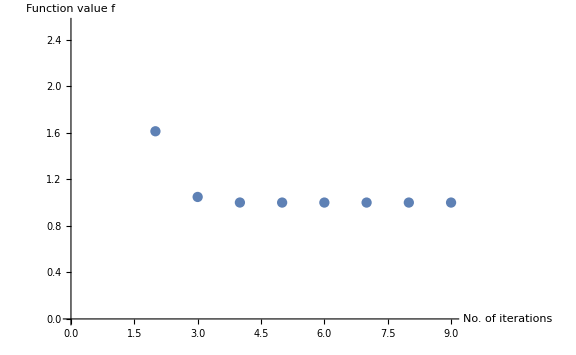

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

0.99987

#### Case 1.2.14: N=100, m=1/10, δ=1, dimS=2, l=48

```mathematica
CM0=partialCM[100,1/10,1,48,2,2];CM0//MatrixForm
```

(1.28101 | 0 | -0.41982 | 0 | -5.16558×10^-6 | 0 | -5.21181×10^-6 | 0
0 | 1.39418 | 0 | 0.760649 | 0 | 0.00235308 | 0 | 0.00236743
-0.41982 | 0 | 1.28101 | 0 | -5.21181×10^-6 | 0 | -5.16558×10^-6 | 0
0 | 0.760649 | 0 | 1.39418 | 0 | 0.00236743 | 0 | 0.00235308
-5.16558×10^-6 | 0 | -5.21181×10^-6 | 0 | 1.28101 | 0 | -0.41982 | 0
0 | 0.00235308 | 0 | 0.00236743 | 0 | 1.39418 | 0 | 0.760649
-5.21181×10^-6 | 0 | -5.16558×10^-6 | 0 | -0.41982 | 0 | 1.28101 | 0
0 | 0.00236743 | 0 | 0.00235308 | 0 | 0.760649 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,(2+2),"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[4(2+2)],"qpqp","qpqp"];
```

{{0.414485,0.412881,0.137503,0.137461},{{0.,-0.397331,0.,-0.397331,0.,-0.397331,0.,-0.397331},{0.629199,0.,0.629199,0.,0.629199,0.,0.629199,0.},{0.,-0.397769,0.,-0.397769,0.,0.397769,0.,0.397769},{0.628506,0.,0.628506,0.,-0.628506,0.,-0.628506,0.},{0.390616,0.,-0.390616,0.,-0.390616,0.,0.390616,0.},{0.,0.640015,0.,-0.640015,0.,-0.640015,0.,0.640015},{0.390611,0.,-0.390611,0.,0.390611,0.,-0.390611,0.},{0.,0.640022,0.,-0.640022,0.,0.640022,0.,-0.640022}}}

SparseArray[…]

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4(2),"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(2+2),(2+2)},10^-9,∞];
```

Final value: 0.99987

Number of iterations: 9

Number of total corrections: 0

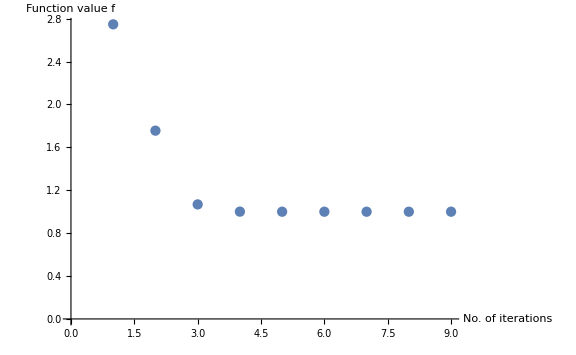

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

0.99987

#### Summary Case 1.2

```mathematica
listCase12={{0,0.8907375335066201},{1,0.9565937985206172},{2,0.9738019994613343},{3,0.982673119719363},{4,0.9879949368237251},{5,0.9914320951322009},{8,0.9965233529563681},{10,0.9979697604259276},{15,0.9993623138824264},{20,0.9997234483230049},{30,0.9998568167242625},{40,0.9998693733738202},{45,0.9998702749184759},{48,0.9998703891905889}};
```

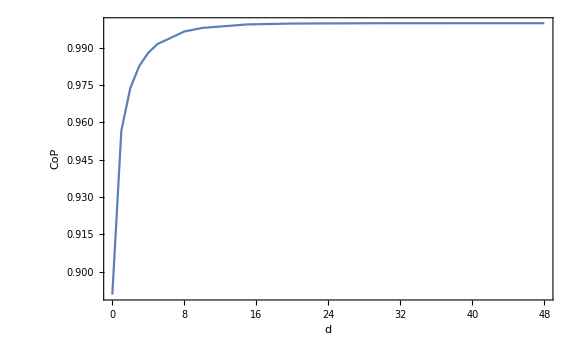

```mathematica
ListPlot[listCase12,PlotRange->All, Joined->True,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50]
```

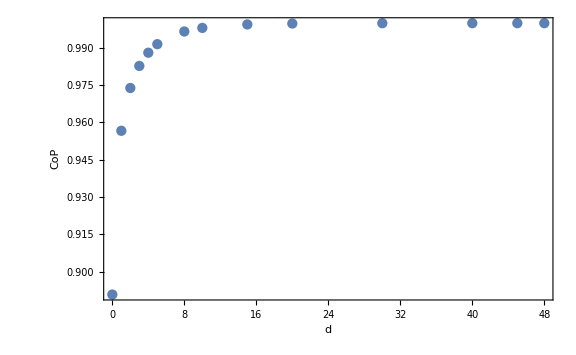
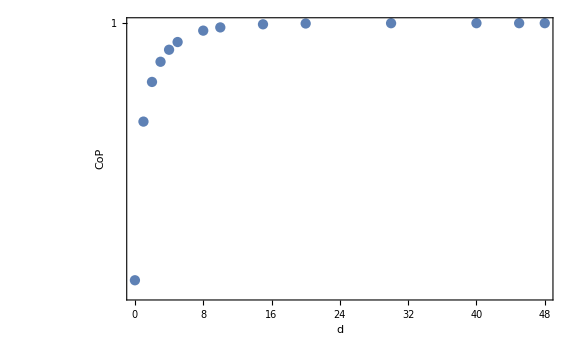

```mathematica
PlotlistCase12=Row[{ListPlot[listCase12,PlotRange->All,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50],ListLogPlot[listCase12,PlotRange->All,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50]}]
Export[NotebookDirectory[]<>"PlotlistCase12.pdf",PlotlistCase12];
```

### Case 1.3: N=100, m=1/10, δ=1, dimS=3

#### Case 1.3.1: N=100, m=1/10, δ=1, dimS=3, l=0

```mathematica
CM0=partialCM[100,1/10,1,0,3,3];CM0//MatrixForm
```

(1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.0106767 | 0
0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.293694
-0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0
0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884
-0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0
0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315
-0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0
0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542
-0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0
0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649
-0.0106767 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0
0 | 0.293694 | 0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,(3+3),"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[4(3+3)],"qpqp","qpqp"];
```

{{0.393413,0.253958,0.0303521,0.00965265,0.000795038,0.000113332},{{0.,0.464828,0.,0.134223,0.,0.0864634,0.,0.0864634,0.,0.134223,0.,0.464828},{-0.769132,0.,-0.66172,0.,-0.6207,0.,-0.6207,0.,-0.66172,0.,-0.769132,0.},{0.,0.653325,0.,0.134353,0.,0.0321798,0.,-0.0321798,0.,-0.134353,0.,-0.653325},{-0.686934,0.,-0.354492,0.,-0.111304,0.,0.111304,0.,0.354492,0.,0.686934,0.},{0.,-0.566478,0.,0.327234,0.,0.353083,0.,0.353083,0.,0.327234,0.,-0.566478},{0.241485,0.,-0.430893,0.,-0.629317,0.,-0.629317,0.,-0.430893,0.,0.241485,0.},{-0.126864,0.,0.557757,0.,0.246952,0.,-0.246952,0.,-0.557757,0.,0.126864,0.},{0.,-0.399904,0.,0.700438,0.,0.237261,0.,-0.237261,0.,-0.700438,0.,0.399904},{-0.0344984,0.,0.384944,0.,-0.412111,0.,-0.412111,0.,0.384944,0.,-0.0344984,0.},{0.,-0.164945,0.,0.701866,0.,-0.543861,0.,-0.543861,0.,0.701866,0.,-0.164945},{-0.00897789,0.,0.161422,0.,-0.491679,0.,0.491679,0.,-0.161422,0.,0.00897789,0.},{0.,-0.0529604,0.,0.382218,0.,-0.890471,0.,0.890471,0.,-0.382218,0.,0.0529604}}}

SparseArray[…]

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4(3),"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(3+3),(3+3)},10^-9,∞];
```

Final value: 1.0354

Number of iterations: 10

Number of total corrections: 0

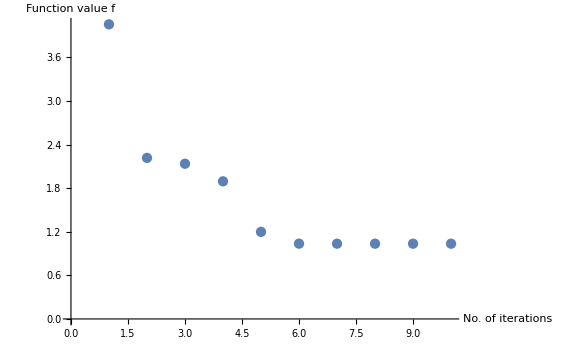

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

1.0354

#### Case 1.3.2: N=100, m=1/10, δ=1, dimS=3, l=1

```mathematica
CM0=partialCM[100,1/10,1,1,3,3];CM0//MatrixForm
```

(1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0177027 | 0 | -0.0106767 | 0 | -0.00697557 | 0
0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.353884 | 0 | 0.293694 | 0 | 0.247118
-0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.0106767 | 0
0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.293694
-0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0
0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884
-0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0
0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542
-0.0106767 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0
0 | 0.293694 | 0 | 0.353884 | 0 | 0.435315 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649
-0.00697557 | 0 | -0.0106767 | 0 | -0.0177027 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0
0 | 0.247118 | 0 | 0.293694 | 0 | 0.353884 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,(3+3),"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[4(3+3)],"qpqp","qpqp"];
```

{{0.487641,0.266758,0.201283,0.0126127,0.0120973,0.000233834},{{0.,0.288111,0.,0.131376,0.,0.340432,0.,0.340432,0.,0.131376,0.,0.288111},{-0.607889,0.,-0.62104,0.,-0.714596,0.,-0.714596,0.,-0.62104,0.,-0.607889,0.},{0.,-0.629703,0.,-0.137445,0.,-0.0460643,0.,0.0460643,0.,0.137445,0.,0.629703},{0.694522,0.,0.39452,0.,0.18307,0.,-0.18307,0.,-0.39452,0.,-0.694522,0.},{-0.475034,0.,-0.0484566,0.,0.420726,0.,0.420726,0.,-0.0484566,0.,-0.475034,0.},{0.,-0.578503,0.,-0.0438156,0.,0.530198,0.,0.530198,0.,-0.0438156,0.,-0.578503},{-0.129622,0.,0.535978,0.,-0.0971383,0.,-0.0971383,0.,0.535978,0.,-0.129622,0.},{0.,-0.386136,0.,0.776688,0.,-0.346526,0.,-0.346526,0.,0.776688,0.,-0.386136},{0.143635,0.,-0.53435,0.,-0.36912,0.,0.36912,0.,0.53435,0.,-0.143635,0.},{0.,0.426987,0.,-0.609935,0.,-0.305458,0.,0.305458,0.,0.609935,0.,-0.426987},{0.0155292,0.,-0.23708,0.,0.495107,0.,-0.495107,0.,0.23708,0.,-0.0155292,0.},{0.,0.0854969,0.,-0.50555,0.,0.765119,0.,-0.765119,0.,0.50555,0.,-0.0854969}}}

SparseArray[…]

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4(3),"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(3+3),(3+3)},10^-9,∞];
```

Final value: 1.09587

Number of iterations: 9

Number of total corrections: 0

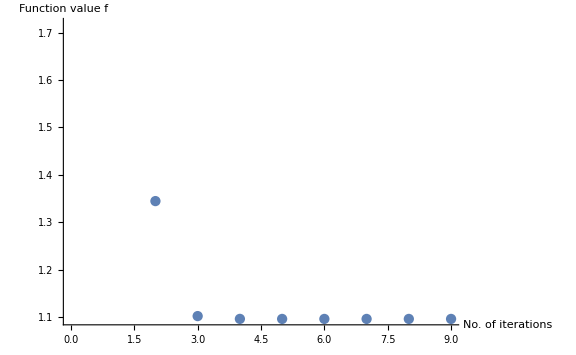

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

1.09587

#### Case 1.3.3: N=100, m=1/10, δ=1, dimS=3, l=2

```mathematica
CM0=partialCM[100,1/10,1,2,3,3];CM0//MatrixForm
```

(1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0106767 | 0 | -0.00697557 | 0 | -0.0048107 | 0
0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.293694 | 0 | 0.247118 | 0 | 0.209989
-0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0177027 | 0 | -0.0106767 | 0 | -0.00697557 | 0
0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.353884 | 0 | 0.293694 | 0 | 0.247118
-0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.0106767 | 0
0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.293694
-0.0106767 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0
0 | 0.293694 | 0 | 0.353884 | 0 | 0.435315 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542
-0.00697557 | 0 | -0.0106767 | 0 | -0.0177027 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0
0 | 0.247118 | 0 | 0.293694 | 0 | 0.353884 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649
-0.0048107 | 0 | -0.00697557 | 0 | -0.0106767 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0
0 | 0.209989 | 0 | 0.247118 | 0 | 0.293694 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,(3+3),"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[4(3+3)],"qpqp","qpqp"];
```

{{0.490822,0.284201,0.198414,0.118019,0.0116615,0.00930244},{{0.,0.285109,0.,0.141438,0.,0.355596,0.,0.355596,0.,0.141438,0.,0.285109},{-0.592423,0.,-0.606122,0.,-0.690013,0.,-0.690013,0.,-0.606122,0.,-0.592423,0.},{0.,0.580859,0.,0.142929,0.,0.137343,0.,-0.137343,0.,-0.142929,0.,-0.580859},{-0.683633,0.,-0.438657,0.,-0.292767,0.,0.292767,0.,0.438657,0.,0.683633,0.},{-0.483822,0.,-0.0442017,0.,0.405499,0.,0.405499,0.,-0.0442017,0.,-0.483822,0.},{0.,-0.588916,0.,-0.0250729,0.,0.527649,0.,0.527649,0.,-0.0250729,0.,-0.588916},{-0.180561,0.,0.154493,0.,0.602865,0.,-0.602865,0.,-0.154493,0.,0.180561,0.},{0.,-0.32933,0.,0.0308151,0.,0.72284,0.,-0.72284,0.,-0.0308151,0.,0.32933},{-0.123437,0.,0.531675,0.,-0.112505,0.,-0.112505,0.,0.531675,0.,-0.123437,0.},{0.,-0.373992,0.,0.777097,0.,-0.361521,0.,-0.361521,0.,0.777097,0.,-0.373992},{0.116938,0.,-0.548914,0.,0.076678,0.,-0.076678,0.,0.548914,0.,-0.116938,0.},{0.,0.371495,0.,-0.787998,0.,0.3132,0.,-0.3132,0.,0.787998,0.,-0.371495}}}

SparseArray[…]

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4(3),"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(3+3),(3+3)},10^-9,∞];
```

Final value: 1.11317

Number of iterations: 9

Number of total corrections: 1

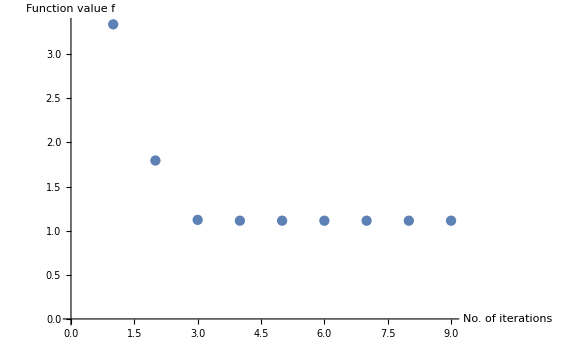

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

1.11317

#### Case 1.3.4: N=100, m=1/10, δ=1, dimS=3, l=3

```mathematica
CM0=partialCM[100,1/10,1,3,3,3];CM0//MatrixForm
```

(1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.00697557 | 0 | -0.0048107 | 0 | -0.00344953 | 0
0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.247118 | 0 | 0.209989 | 0 | 0.179771
-0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0106767 | 0 | -0.00697557 | 0 | -0.0048107 | 0
0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.293694 | 0 | 0.247118 | 0 | 0.209989
-0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.0177027 | 0 | -0.0106767 | 0 | -0.00697557 | 0
0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.353884 | 0 | 0.293694 | 0 | 0.247118
-0.00697557 | 0 | -0.0106767 | 0 | -0.0177027 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0
0 | 0.247118 | 0 | 0.293694 | 0 | 0.353884 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542
-0.0048107 | 0 | -0.00697557 | 0 | -0.0106767 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0
0 | 0.209989 | 0 | 0.247118 | 0 | 0.293694 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649
-0.00344953 | 0 | -0.0048107 | 0 | -0.00697557 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0
0 | 0.179771 | 0 | 0.209989 | 0 | 0.247118 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,(3+3),"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[4(3+3)],"qpqp","qpqp"];
```

{{0.484977,0.302442,0.19528,0.14809,0.0124742,0.009514},{{0.,0.290822,0.,0.147149,0.,0.358219,0.,0.358219,0.,0.147149,0.,0.290822},{-0.588506,0.,-0.597618,0.,-0.672524,0.,-0.672524,0.,-0.597618,0.,-0.588506,0.},{0.,0.528553,0.,0.147111,0.,0.211768,0.,-0.211768,0.,-0.147111,0.,-0.528553},{-0.662964,0.,-0.47004,0.,-0.37985,0.,0.37985,0.,0.47004,0.,0.662964,0.},{0.481644,0.,0.0363619,0.,-0.405961,0.,-0.405961,0.,0.0363619,0.,0.481644,0.},{0.,0.590153,0.,0.0153822,0.,-0.530094,0.,-0.530094,0.,0.0153822,0.,0.590153},{-0.260853,0.,0.11431,0.,0.571657,0.,-0.571657,0.,-0.11431,0.,0.260853,0.},{0.,-0.407018,0.,0.0206819,0.,0.684788,0.,-0.684788,0.,-0.0206819,0.,0.407018},{-0.120968,0.,0.529524,0.,-0.119308,0.,-0.119308,0.,0.529524,0.,-0.120968,0.},{0.,-0.368745,0.,0.777117,0.,-0.367884,0.,-0.367884,0.,0.777117,0.,-0.368745},{-0.117228,0.,0.545188,0.,-0.0861423,0.,0.0861423,0.,-0.545188,0.,0.117228,0.},{0.,-0.370359,0.,0.785945,0.,-0.326158,0.,0.326158,0.,-0.785945,0.,0.370359}}}

SparseArray[…]

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4(3),"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(3+3),(3+3)},10^-9,∞];
```

Final value: 1.12242

Number of iterations: 8

Number of total corrections: 0

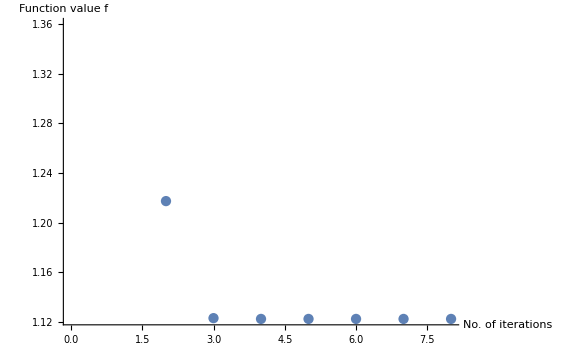

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

1.12242

#### Case 1.3.5: N=100, m=1/10, δ=1, dimS=3, l=5

```mathematica
CM0=partialCM[100,1/10,1,5,3,3];CM0//MatrixForm
```

(1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.00344953 | 0 | -0.00254724 | 0 | -0.00192459 | 0
0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.179771 | 0 | 0.154799 | 0 | 0.133923
-0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0048107 | 0 | -0.00344953 | 0 | -0.00254724 | 0
0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.209989 | 0 | 0.179771 | 0 | 0.154799
-0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.00697557 | 0 | -0.0048107 | 0 | -0.00344953 | 0
0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.247118 | 0 | 0.209989 | 0 | 0.179771
-0.00344953 | 0 | -0.0048107 | 0 | -0.00697557 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0
0 | 0.179771 | 0 | 0.209989 | 0 | 0.247118 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542
-0.00254724 | 0 | -0.00344953 | 0 | -0.0048107 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0
0 | 0.154799 | 0 | 0.179771 | 0 | 0.209989 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649
-0.00192459 | 0 | -0.00254724 | 0 | -0.00344953 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0
0 | 0.133923 | 0 | 0.154799 | 0 | 0.179771 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,(3+3),"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[4(3+3)],"qpqp","qpqp"];
```

{{0.470471,0.332902,0.191476,0.169796,0.0141584,0.0102293},{{0.,-0.303333,0.,-0.152753,0.,-0.358001,0.,-0.358001,0.,-0.152753,0.,-0.303333},{0.586758,0.,0.586321,0.,0.649312,0.,0.649312,0.,0.586321,0.,0.586758,0.},{0.,0.45562,0.,0.151281,0.,0.288489,0.,-0.288489,0.,-0.151281,0.,-0.45562},{-0.629266,0.,-0.502955,0.,-0.475604,0.,0.475604,0.,0.502955,0.,0.629266,0.},{0.474122,0.,0.025439,0.,-0.412577,0.,-0.412577,0.,0.025439,0.,0.474122,0.},{0.,0.587098,0.,0.0069248,0.,-0.536791,0.,-0.536791,0.,0.0069248,0.,0.587098},{0.34957,0.,-0.061922,0.,-0.519617,0.,0.519617,0.,0.061922,0.,-0.34957,0.},{0.,0.486463,0.,-0.00921973,0.,-0.633883,0.,0.633883,0.,0.00921973,0.,-0.486463},{0.119548,0.,-0.527872,0.,0.123942,0.,0.123942,0.,-0.527872,0.,0.119548,0.},{0.,0.365213,0.,-0.777198,0.,0.371772,0.,0.371772,0.,-0.777198,0.,0.365213},{0.117388,0.,-0.540326,0.,0.0979465,0.,-0.0979465,0.,0.540326,0.,-0.117388,0.},{0.,0.368359,0.,-0.783493,0.,0.34118,0.,-0.34118,0.,0.783493,0.,-0.368359}}}

SparseArray[…]

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4(3),"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(3+3),(3+3)},10^-9,∞];
```

Final value: 1.13188

Number of iterations: 9

Number of total corrections: 0

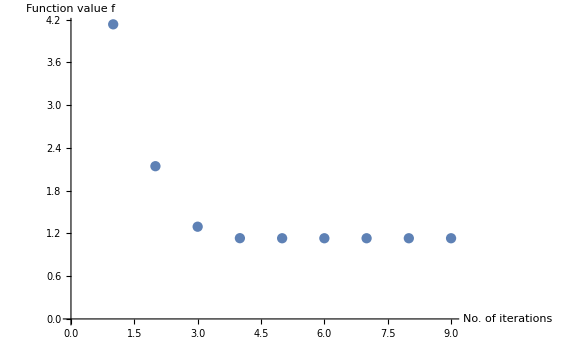

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

1.13188

#### Case 1.3.6: N=100, m=1/10, δ=1, dimS=3, l=8

```mathematica
CM0=partialCM[100,1/10,1,8,3,3];CM0//MatrixForm
```

(1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0014811 | 0 | -0.00115709 | 0 | -0.000915362 | 0
0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.116311 | 0 | 0.101343 | 0 | 0.0885453
-0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.00192459 | 0 | -0.0014811 | 0 | -0.00115709 | 0
0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.133923 | 0 | 0.116311 | 0 | 0.101343
-0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.00254724 | 0 | -0.00192459 | 0 | -0.0014811 | 0
0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.154799 | 0 | 0.133923 | 0 | 0.116311
-0.0014811 | 0 | -0.00192459 | 0 | -0.00254724 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0
0 | 0.116311 | 0 | 0.133923 | 0 | 0.154799 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542
-0.00115709 | 0 | -0.0014811 | 0 | -0.00192459 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0
0 | 0.101343 | 0 | 0.116311 | 0 | 0.133923 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649
-0.000915362 | 0 | -0.00115709 | 0 | -0.0014811 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0
0 | 0.0885453 | 0 | 0.101343 | 0 | 0.116311 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,(3+3),"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[4(3+3)],"qpqp","qpqp"];
```

{{0.452619,0.362174,0.188786,0.179115,0.0151884,0.0114143},{{0.,0.317715,0.,0.155839,0.,0.356112,0.,0.356112,0.,0.155839,0.,0.317715},{-0.586948,0.,-0.575487,0.,-0.628551,0.,-0.628551,0.,-0.575487,0.,-0.586948,0.},{0.,0.404818,0.,0.153755,0.,0.326403,0.,-0.326403,0.,-0.153755,0.,-0.404818},{-0.60671,0.,-0.524283,0.,-0.532416,0.,0.532416,0.,0.524283,0.,0.60671,0.},{0.464733,0.,0.016221,0.,-0.421723,0.,-0.421723,0.,0.016221,0.,0.464733,0.},{0.,0.581083,0.,0.00277285,0.,-0.545161,0.,-0.545161,0.,0.00277285,0.,0.581083},{0.399581,0.,-0.0293371,0.,-0.481756,0.,0.481756,0.,0.0293371,0.,-0.399581,0.},{0.,0.528696,0.,-0.00337196,0.,-0.599151,0.,0.599151,0.,0.00337196,0.,-0.528696},{0.1193,0.,-0.527665,0.,0.124477,0.,0.124477,0.,-0.527665,0.,0.1193,0.},{0.,0.364373,0.,-0.777523,0.,0.371627,0.,0.371627,0.,-0.777523,0.,0.364373},{-0.117622,0.,0.536426,0.,-0.106809,0.,0.106809,0.,-0.536426,0.,0.117622,0.},{0.,-0.366739,0.,0.781636,0.,-0.351782,0.,0.351782,0.,-0.781636,0.,0.366739}}}

SparseArray[…]

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4(3),"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(3+3),(3+3)},10^-9,∞];
```

Final value: 1.13761

Number of iterations: 8

Number of total corrections: 0

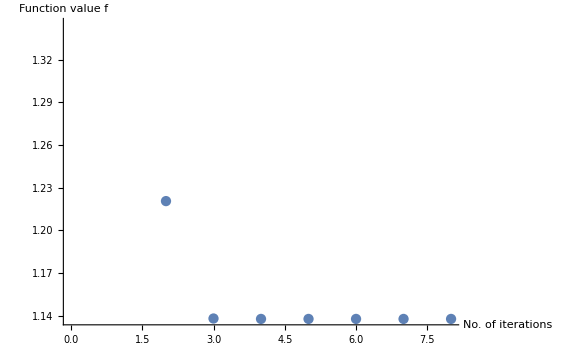

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

1.13761

#### Case 1.3.7: N=100, m=1/10, δ=1, dimS=3, l=10

```mathematica
CM0=partialCM[100,1/10,1,10,3,3];CM0//MatrixForm
```

(1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.000915362 | 0 | -0.000731856 | 0 | -0.000590478 | 0
0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.0885453 | 0 | 0.0775485 | 0 | 0.0680592
-0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.00115709 | 0 | -0.000915362 | 0 | -0.000731856 | 0
0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.101343 | 0 | 0.0885453 | 0 | 0.0775485
-0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.0014811 | 0 | -0.00115709 | 0 | -0.000915362 | 0
0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.116311 | 0 | 0.101343 | 0 | 0.0885453
-0.000915362 | 0 | -0.00115709 | 0 | -0.0014811 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0
0 | 0.0885453 | 0 | 0.101343 | 0 | 0.116311 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542
-0.000731856 | 0 | -0.000915362 | 0 | -0.00115709 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0
0 | 0.0775485 | 0 | 0.0885453 | 0 | 0.101343 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649
-0.000590478 | 0 | -0.000731856 | 0 | -0.000915362 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0
0 | 0.0680592 | 0 | 0.0775485 | 0 | 0.0885453 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,(3+3),"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[4(3+3)],"qpqp","qpqp"];
```

{{0.443786,0.37457,0.187824,0.181474,0.0153554,0.012045},{{0.,0.324702,0.,0.156621,0.,0.354976,0.,0.354976,0.,0.156621,0.,0.324702},{-0.58739,0.,-0.570512,0.,-0.619531,0.,-0.619531,0.,-0.570512,0.,-0.58739,0.},{0.,0.387991,0.,0.154593,0.,0.335965,0.,-0.335965,0.,-0.154593,0.,-0.387991},{-0.600231,0.,-0.53199,0.,-0.550277,0.,0.550277,0.,0.53199,0.,0.600231,0.},{0.46009,0.,0.0123661,0.,-0.426307,0.,-0.426307,0.,0.0123661,0.,0.46009,0.},{0.,0.577727,0.,0.00168325,0.,-0.549305,0.,-0.549305,0.,0.00168325,0.,0.577727},{0.414207,0.,-0.0194997,0.,-0.469377,0.,0.469377,0.,0.0194997,0.,-0.414207,0.},{0.,0.540756,0.,-0.00194599,0.,-0.587964,0.,0.587964,0.,0.00194599,0.,-0.540756},{0.119281,0.,-0.527957,0.,0.123835,0.,0.123835,0.,-0.527957,0.,0.119281,0.},{0.,0.364406,0.,-0.777762,0.,0.370722,0.,0.370722,0.,-0.777762,0.,0.364406},{0.117789,0.,-0.534899,0.,0.110102,0.,-0.110102,0.,0.534899,0.,-0.117789,0.},{0.,0.366168,0.,-0.780933,0.,0.355572,0.,-0.355572,0.,0.780933,0.,-0.366168}}}

SparseArray[…]

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4(3),"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(3+3),(3+3)},10^-9,∞];
```

Final value: 1.13931

Number of iterations: 9

Number of total corrections: 0

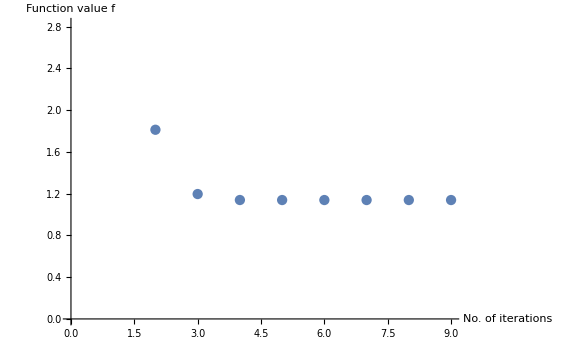

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

1.13931

#### Case 1.3.8: N=100, m=1/10, δ=1, dimS=3, l=15

```mathematica
CM0=partialCM[100,1/10,1,15,3,3];CM0//MatrixForm
```

(1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.00032389 | 0 | -0.000268258 | 0 | -0.000223255 | 0
0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.0464815 | 0 | 0.0410507 | 0 | 0.0362986
-0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.000393171 | 0 | -0.00032389 | 0 | -0.000268258 | 0
0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.0527011 | 0 | 0.0464815 | 0 | 0.0410507
-0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.000480174 | 0 | -0.000393171 | 0 | -0.00032389 | 0
0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.0598408 | 0 | 0.0527011 | 0 | 0.0464815
-0.00032389 | 0 | -0.000393171 | 0 | -0.000480174 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0
0 | 0.0464815 | 0 | 0.0527011 | 0 | 0.0598408 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542
-0.000268258 | 0 | -0.00032389 | 0 | -0.000393171 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0
0 | 0.0410507 | 0 | 0.0464815 | 0 | 0.0527011 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649
-0.000223255 | 0 | -0.000268258 | 0 | -0.00032389 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0
0 | 0.0362986 | 0 | 0.0410507 | 0 | 0.0464815 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,(3+3),"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[4(3+3)],"qpqp","qpqp"];
```

{{0.429294,0.392665,0.186552,0.18387,0.0152167,0.0130845},{{0.,-0.33618,0.,-0.157164,0.,-0.352908,0.,-0.352908,0.,-0.157164,0.,-0.33618},{0.588452,0.,0.562565,0.,0.605707,0.,0.605707,0.,0.562565,0.,0.588452,0.},{0.,-0.367418,0.,-0.155682,0.,-0.345203,0.,0.345203,0.,0.155682,0.,0.367418},{0.593654,0.,0.542518,0.,0.571896,0.,-0.571896,0.,-0.542518,0.,-0.593654,0.},{-0.452408,0.,-0.00653595,0.,0.433874,0.,0.433874,0.,-0.00653595,0.,-0.452408,0.},{0.,-0.571854,0.,-0.000596745,0.,0.556118,0.,0.556118,0.,-0.000596745,0.,-0.571854},{0.430687,0.,-0.00833143,0.,-0.454645,0.,0.454645,0.,0.00833143,0.,-0.430687,0.},{0.,0.554236,0.,-0.000636749,0.,-0.574718,0.,0.574718,0.,0.000636749,0.,-0.554236},{-0.119181,0.,0.52885,0.,-0.121986,0.,-0.121986,0.,0.52885,0.,-0.119181,0.},{0.,-0.364679,0.,0.778256,0.,-0.368534,0.,-0.368534,0.,0.778256,0.,-0.364679},{0.118142,0.,-0.532756,0.,0.114522,0.,-0.114522,0.,0.532756,0.,-0.118142,0.},{0.,0.365483,0.,-0.779971,0.,0.360516,0.,-0.360516,0.,0.779971,0.,-0.365483}}}

SparseArray[…]

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4(3),"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(3+3),(3+3)},10^-9,∞];
```

Final value: 1.14101

Number of iterations: 9

Number of total corrections: 0

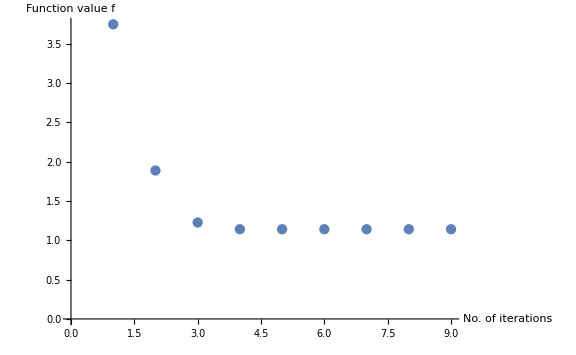

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

1.14101

#### Case 1.3.9: N=100, m=1/10, δ=1, dimS=3, l=20

```mathematica
CM0=partialCM[100,1/10,1,20,3,3];CM0//MatrixForm
```

(1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.000131877 | 0 | -0.000111427 | 0 | -0.0000944326 | 0
0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.0252583 | 0 | 0.0224262 | 0 | 0.0199298
-0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.000156594 | 0 | -0.000131877 | 0 | -0.000111427 | 0
0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.0284749 | 0 | 0.0252583 | 0 | 0.0224262
-0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.00018661 | 0 | -0.000156594 | 0 | -0.000131877 | 0
0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.0321328 | 0 | 0.0284749 | 0 | 0.0252583
-0.000131877 | 0 | -0.000156594 | 0 | -0.00018661 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0
0 | 0.0252583 | 0 | 0.0284749 | 0 | 0.0321328 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542
-0.000111427 | 0 | -0.000131877 | 0 | -0.000156594 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0
0 | 0.0224262 | 0 | 0.0252583 | 0 | 0.0284749 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649
-0.0000944326 | 0 | -0.000111427 | 0 | -0.000131877 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0
0 | 0.0199298 | 0 | 0.0224262 | 0 | 0.0252583 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,(3+3),"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[4(3+3)],"qpqp","qpqp"];
```

{{0.421469,0.401467,0.185981,0.184686,0.0149372,0.0136413},{{0.,0.342429,0.,0.157125,0.,0.351693,0.,0.351693,0.,0.157125,0.,0.342429},{-0.589176,0.,-0.558323,0.,-0.598597,0.,-0.598597,0.,-0.558323,0.,-0.589176,0.},{0.,-0.358893,0.,-0.156173,0.,-0.348082,0.,0.348082,0.,0.156173,0.,0.358893},{0.591572,0.,0.547435,0.,0.580881,0.,-0.580881,0.,-0.547435,0.,-0.591572,0.},{-0.448206,0.,-0.00354532,0.,0.437983,0.,0.437983,0.,-0.00354532,0.,-0.448206,0.},{0.,-0.56852,0.,-0.000250714,0.,0.559806,0.,0.559806,0.,-0.000250714,0.,-0.56852},{-0.437004,0.,0.00405017,0.,0.448759,0.,-0.448759,0.,-0.00405017,0.,0.437004,0.},{0.,-0.559391,0.,0.000257718,0.,0.569443,0.,-0.569443,0.,-0.000257718,0.,0.559391},{0.119047,0.,-0.529523,0.,0.120663,0.,0.120663,0.,-0.529523,0.,0.119047,0.},{0.,0.36486,0.,-0.778573,0.,0.367073,0.,0.367073,0.,-0.778573,0.,0.36486},{0.118373,0.,-0.53174,0.,0.116524,0.,-0.116524,0.,0.53174,0.,-0.118373,0.},{0.,0.365226,0.,-0.779525,0.,0.362694,0.,-0.362694,0.,0.779525,0.,-0.365226}}}

SparseArray[…]

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4(3),"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(3+3),(3+3)},10^-9,∞];
```

Final value: 1.1415

Number of iterations: 10

Number of total corrections: 1

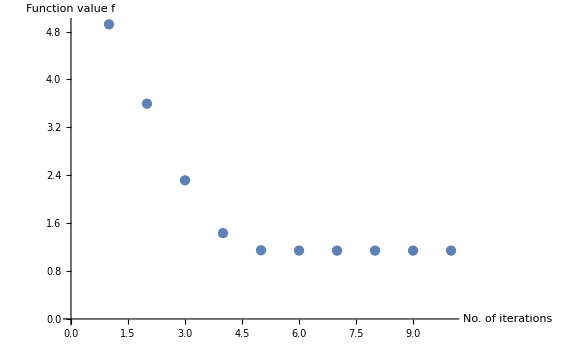

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

1.1415

#### Case 1.3.10: N=100, m=1/10, δ=1, dimS=3, l=30

```mathematica
CM0=partialCM[100,1/10,1,30,3,3];CM0//MatrixForm
```

(1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.000027491 | 0 | -0.0000238043 | 0 | -0.0000206625 | 0
0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.00802546 | 0 | 0.00720207 | 0 | 0.00647449
-0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.000031822 | 0 | -0.000027491 | 0 | -0.0000238043 | 0
0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.00895661 | 0 | 0.00802546 | 0 | 0.00720207
-0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.0000369176 | 0 | -0.000031822 | 0 | -0.000027491 | 0
0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.0100091 | 0 | 0.00895661 | 0 | 0.00802546
-0.000027491 | 0 | -0.000031822 | 0 | -0.0000369176 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0
0 | 0.00802546 | 0 | 0.00895661 | 0 | 0.0100091 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542
-0.0000238043 | 0 | -0.000027491 | 0 | -0.000031822 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0
0 | 0.00720207 | 0 | 0.00802546 | 0 | 0.00895661 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649
-0.0000206625 | 0 | -0.0000238043 | 0 | -0.000027491 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0
0 | 0.00647449 | 0 | 0.00720207 | 0 | 0.00802546 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,(3+3),"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[4(3+3)],"qpqp","qpqp"];
```

{{0.414849,0.408457,0.185556,0.185194,0.014579,0.0141155},{{0.,-0.347766,0.,-0.156916,0.,-0.350606,0.,-0.350606,0.,-0.156916,0.,-0.347766},{0.589875,0.,0.554739,0.,0.592729,0.,0.592729,0.,0.554739,0.,0.589875,0.},{0.,0.35273,0.,0.156558,0.,0.349747,0.,-0.349747,0.,-0.156558,0.,-0.35273},{-0.590387,0.,-0.551273,0.,-0.587415,0.,0.587415,0.,0.551273,0.,0.590387,0.},{0.444606,0.,0.00106784,0.,-0.441483,0.,-0.441483,0.,0.00106784,0.,0.444606,0.},{0.,0.565608,0.,0.0000562221,0.,-0.562937,0.,-0.562937,0.,0.0000562221,0.,0.565608},{0.441354,0.,-0.00111448,0.,-0.44462,0.,0.44462,0.,0.00111448,0.,-0.441354,0.},{0.,0.562948,0.,-0.0000564537,0.,-0.565743,0.,0.565743,0.,0.0000564537,0.,-0.562948},{-0.118872,0.,0.530195,0.,-0.119383,0.,-0.119383,0.,0.530195,0.,-0.118872,0.},{0.,-0.365004,0.,0.778869,0.,-0.365703,0.,-0.365703,0.,0.778869,0.,-0.365004},{-0.118593,0.,0.530934,0.,-0.11806,0.,0.11806,0.,-0.530934,0.,0.118593,0.},{0.,-0.36506,0.,0.77918,0.,-0.364332,0.,0.364332,0.,-0.77918,0.,0.36506}}}

SparseArray[…]

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4(3),"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(3+3),(3+3)},10^-9,∞];
```

Final value: 1.14171

Number of iterations: 9

Number of total corrections: 1

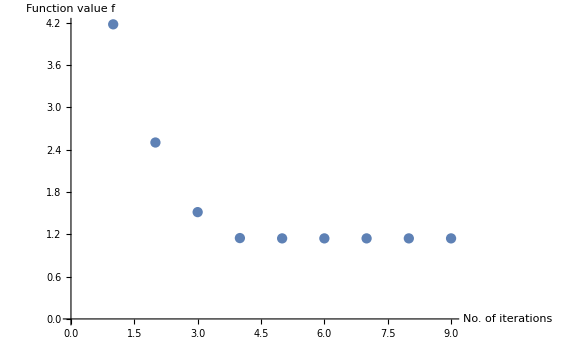

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

1.14171

#### Case 1.3.11: N=100, m=1/10, δ=1, dimS=3, l=40

```mathematica
CM0=partialCM[100,1/10,1,40,3,3];CM0//MatrixForm
```

(1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -7.6322×10^-6 | 0 | -6.93646×10^-6 | 0 | -6.37158×10^-6 | 0
0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.00309418 | 0 | 0.00288986 | 0 | 0.00272137
-0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -8.47426×10^-6 | 0 | -7.6322×10^-6 | 0 | -6.93646×10^-6 | 0
0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.00333708 | 0 | 0.00309418 | 0 | 0.00288986
-0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -9.48153×10^-6 | 0 | -8.47426×10^-6 | 0 | -7.6322×10^-6 | 0
0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.00362182 | 0 | 0.00333708 | 0 | 0.00309418
-7.6322×10^-6 | 0 | -8.47426×10^-6 | 0 | -9.48153×10^-6 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0
0 | 0.00309418 | 0 | 0.00333708 | 0 | 0.00362182 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542
-6.93646×10^-6 | 0 | -7.6322×10^-6 | 0 | -8.47426×10^-6 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0
0 | 0.00288986 | 0 | 0.00309418 | 0 | 0.00333708 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649
-6.37158×10^-6 | 0 | -6.93646×10^-6 | 0 | -7.6322×10^-6 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0
0 | 0.00272137 | 0 | 0.00288986 | 0 | 0.00309418 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,(3+3),"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[4(3+3)],"qpqp","qpqp"];
```

{{0.412907,0.410435,0.185443,0.185313,0.0144485,0.0142582},{{0.,0.349441,0.,0.156821,0.,0.350177,0.,0.350177,0.,0.156821,0.,0.349441},{-0.590197,0.,-0.553688,0.,-0.590934,0.,-0.590934,0.,-0.553688,0.,-0.590197,0.},{0.,-0.350978,0.,-0.156671,0.,-0.350227,0.,0.350227,0.,0.156671,0.,0.350978},{0.59002,0.,0.552349,0.,0.589271,0.,-0.589271,0.,-0.552349,0.,-0.59002,0.},{-0.443433,0.,-0.000275096,0.,0.442624,0.,0.442624,0.,-0.000275096,0.,-0.443433,0.},{0.,-0.564644,0.,-0.0000126052,0.,0.563951,0.,0.563951,0.,-0.0000126052,0.,-0.564644},{-0.442596,0.,0.000279692,0.,0.443419,0.,-0.443419,0.,-0.000279692,0.,0.442596,0.},{0.,-0.563971,0.,0.000012607,0.,0.564676,0.,-0.564676,0.,-0.000012607,0.,0.563971},{-0.118826,0.,0.530412,0.,-0.11896,0.,-0.11896,0.,0.530412,0.,-0.118826,0.},{0.,-0.365068,0.,0.778961,0.,-0.365251,0.,-0.365251,0.,0.778961,0.,-0.365068},{-0.118644,0.,0.530705,0.,-0.118508,0.,0.118508,0.,-0.530705,0.,0.118644,0.},{0.,-0.364995,0.,0.779083,0.,-0.364809,0.,0.364809,0.,-0.779083,0.,0.364995}}}

SparseArray[…]

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4(3),"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(3+3),(3+3)},10^-9,∞];
```

Final value: 1.14174

Number of iterations: 11

Number of total corrections: 0

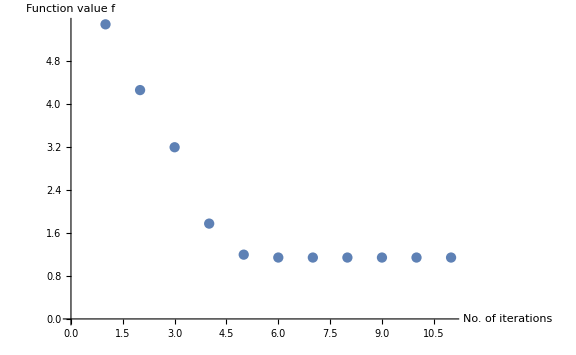

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

1.14174

#### Case 1.3.12: N=100, m=1/10, δ=1, dimS=3, l=47

```mathematica
CM0=partialCM[100,1/10,1,47,3,3];CM0//MatrixForm
```

(1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -5.16558×10^-6 | 0 | -5.21181×10^-6 | 0 | -5.35149×10^-6 | 0
0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.00235308 | 0 | 0.00236743 | 0 | 0.00241066
-0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -5.21181×10^-6 | 0 | -5.16558×10^-6 | 0 | -5.21181×10^-6 | 0
0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.00236743 | 0 | 0.00235308 | 0 | 0.00236743
-0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -5.35149×10^-6 | 0 | -5.21181×10^-6 | 0 | -5.16558×10^-6 | 0
0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.00241066 | 0 | 0.00236743 | 0 | 0.00235308
-5.16558×10^-6 | 0 | -5.21181×10^-6 | 0 | -5.35149×10^-6 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0
0 | 0.00235308 | 0 | 0.00236743 | 0 | 0.00241066 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542
-5.21181×10^-6 | 0 | -5.16558×10^-6 | 0 | -5.21181×10^-6 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0
0 | 0.00236743 | 0 | 0.00235308 | 0 | 0.00236743 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649
-5.35149×10^-6 | 0 | -5.21181×10^-6 | 0 | -5.16558×10^-6 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0
0 | 0.00241066 | 0 | 0.00236743 | 0 | 0.00235308 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
JT=GOPurifyStandardJBoson[rlist,(3+3),"qpqp"]
JR0=GOTransformGtoJ[IdentityMatrix[4(3+3)],"qpqp","qpqp"];
```

{{0.412613,0.410732,0.185427,0.18533,0.0144274,0.0142802},{{0.,0.349903,0.,0.156805,0.,0.349903,0.,0.349903,0.,0.156805,0.,0.349903},{-0.590455,0.,-0.553529,0.,-0.590455,0.,-0.590455,0.,-0.553529,0.,-0.590455,0.},{0.,0.350507,0.,0.156688,0.,0.350507,0.,-0.350507,0.,-0.156688,0.,-0.350507},{-0.589757,0.,-0.55251,0.,-0.589757,0.,0.589757,0.,0.55251,0.,0.589757,0.},{0.443026,0.,0.,0.,-0.443026,0.,-0.443026,0.,0.,0.,0.443026,0.},{0.,0.564301,0.,0.,0.,-0.564301,0.,-0.564301,0.,0.,0.,0.564301},{-0.443011,0.,0.,0.,0.443011,0.,-0.443011,0.,0.,0.,0.443011,0.},{0.,-0.56432,0.,0.,0.,0.56432,0.,-0.56432,0.,0.,0.,0.56432},{-0.118856,0.,0.530446,0.,-0.118856,0.,-0.118856,0.,0.530446,0.,-0.118856,0.},{0.,-0.36513,0.,0.778975,0.,-0.36513,0.,-0.36513,0.,0.778975,0.,-0.36513},{-0.118613,0.,0.53067,0.,-0.118613,0.,0.118613,0.,-0.53067,0.,0.118613,0.},{0.,-0.364933,0.,0.779068,0.,-0.364933,0.,0.364933,0.,-0.779068,0.,0.364933}}}

SparseArray[…]

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4(3),"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(3+3),(3+3)},10^-9,∞];
```

Final value: 1.14175

Number of iterations: 9

Number of total corrections: 1

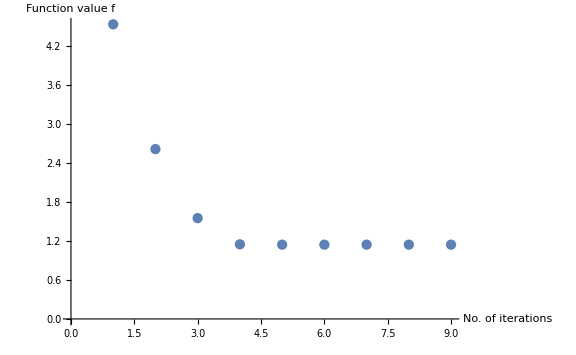

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

```mathematica
N[Result[[1]],16]
```

1.14175

#### Summary Case 1.3

```mathematica
listCase13={{0,1.0353996949506774},{1,1.0958670747421804},{2,1.1131666698812772},{3,1.122422627370193},{5,1.131881609255603},{8,1.137614589740662},{10,1.1393068517535765},{15,1.141010771014572},{20,1.141495464571084},{30,1.1417101572000095},{40,1.141742587423367},{47,1.1417463579004707}};
```

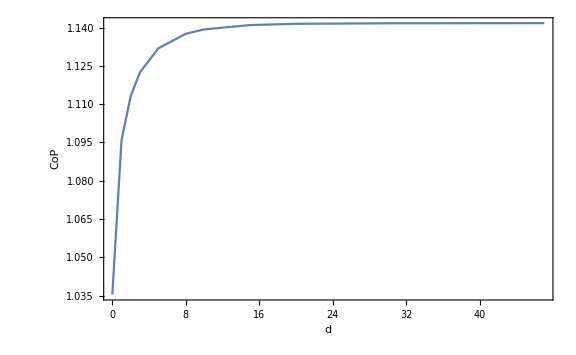

```mathematica
ListPlot[listCase13,PlotRange->All, Joined->True,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50]
```

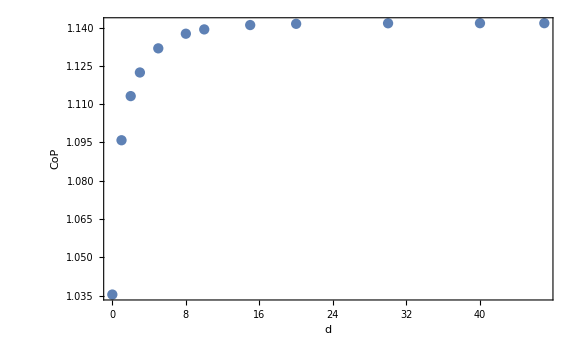
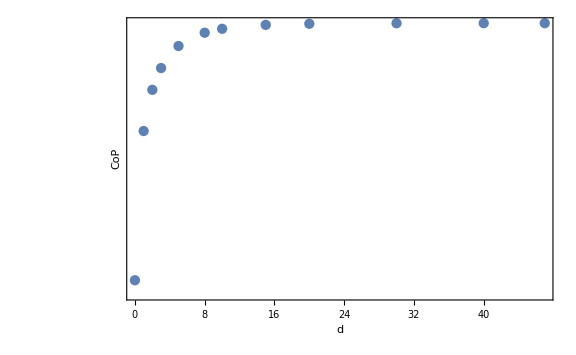

```mathematica
PlotlistCase13=Row[{ListPlot[listCase13,PlotRange->All,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50],ListLogPlot[listCase13,PlotRange->All,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50]}]
Export[NotebookDirectory[]<>"PlotlistCase13.pdf",PlotlistCase13];
```

### Case 1.4: N=100, m=1/10, δ=1, dimS=8

#### Case 1.4.1: N=100, m=1/10, δ=1, dimS=8, l=0

```mathematica
CM0=partialCM[100,1/10,1,0,6,6];CM0//MatrixForm
```

(1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.0106767 | 0 | -0.00697557 | 0 | -0.0048107 | 0 | -0.00344953 | 0 | -0.00254724 | 0 | -0.00192459 | 0 | -0.0014811 | 0
0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.293694 | 0 | 0.247118 | 0 | 0.209989 | 0 | 0.179771 | 0 | 0.154799 | 0 | 0.133923 | 0 | 0.116311
-0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.0106767 | 0 | -0.00697557 | 0 | -0.0048107 | 0 | -0.00344953 | 0 | -0.00254724 | 0 | -0.00192459 | 0
0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.293694 | 0 | 0.247118 | 0 | 0.209989 | 0 | 0.179771 | 0 | 0.154799 | 0 | 0.133923
-0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.0106767 | 0 | -0.00697557 | 0 | -0.0048107 | 0 | -0.00344953 | 0 | -0.00254724 | 0
0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.293694 | 0 | 0.247118 | 0 | 0.209989 | 0 | 0.179771 | 0 | 0.154799
-0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.0106767 | 0 | -0.00697557 | 0 | -0.0048107 | 0 | -0.00344953 | 0
0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.293694 | 0 | 0.247118 | 0 | 0.209989 | 0 | 0.179771
-0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.0106767 | 0 | -0.00697557 | 0 | -0.0048107 | 0
0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.293694 | 0 | 0.247118 | 0 | 0.209989
-0.0106767 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.0106767 | 0 | -0.00697557 | 0
0 | 0.293694 | 0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.293694 | 0 | 0.247118
-0.00697557 | 0 | -0.0106767 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0 | -0.0106767 | 0
0 | 0.247118 | 0 | 0.293694 | 0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884 | 0 | 0.293694
-0.0048107 | 0 | -0.00697557 | 0 | -0.0106767 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0 | -0.0177027 | 0
0 | 0.209989 | 0 | 0.247118 | 0 | 0.293694 | 0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315 | 0 | 0.353884
-0.00344953 | 0 | -0.0048107 | 0 | -0.00697557 | 0 | -0.0106767 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0 | -0.0334432 | 0
0 | 0.179771 | 0 | 0.209989 | 0 | 0.247118 | 0 | 0.293694 | 0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542 | 0 | 0.435315
-0.00254724 | 0 | -0.00344953 | 0 | -0.0048107 | 0 | -0.00697557 | 0 | -0.0106767 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0 | -0.0813337 | 0
0 | 0.154799 | 0 | 0.179771 | 0 | 0.209989 | 0 | 0.247118 | 0 | 0.293694 | 0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649 | 0 | 0.554542
-0.00192459 | 0 | -0.00254724 | 0 | -0.00344953 | 0 | -0.0048107 | 0 | -0.00697557 | 0 | -0.0106767 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0 | -0.41982 | 0
0 | 0.133923 | 0 | 0.154799 | 0 | 0.179771 | 0 | 0.209989 | 0 | 0.247118 | 0 | 0.293694 | 0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418 | 0 | 0.760649
-0.0014811 | 0 | -0.00192459 | 0 | -0.00254724 | 0 | -0.00344953 | 0 | -0.0048107 | 0 | -0.00697557 | 0 | -0.0106767 | 0 | -0.0177027 | 0 | -0.0334432 | 0 | -0.0813337 | 0 | -0.41982 | 0 | 1.28101 | 0
0 | 0.116311 | 0 | 0.133923 | 0 | 0.154799 | 0 | 0.179771 | 0 | 0.209989 | 0 | 0.247118 | 0 | 0.293694 | 0 | 0.353884 | 0 | 0.435315 | 0 | 0.554542 | 0 | 0.760649 | 0 | 1.39418)

```mathematica
{rlist,MTra}=GOExtractStdFormG[CM0]
```

Dot::dotsh: Tensors … and {{-0.0000673755,-0.000754797,0.00432532,0.0175911,-0.0491097,-0.131737,0.218664,0.467473,-0.470667,-0.893776,0.499209,0.924417,-0.18773,-0.40969,-0.0993056,-0.105545,0.1213,0.210168,-0.0414285,-0.0945,0.0049811,0.0173532,-0.000104762,-0.000992942},{«23»,«22»,-«22»},«21»,{-0.0000205719,«22»,-0.000322678}} have incompatible shapes.

{{0.716874,0.365263,0.303172,0.0592682,0.0386052,0.0210521,0.00927665,0.00272026,0.+0.00162623 ⅈ,0.+0.00921594 ⅈ,0.+0.0651395 ⅈ,0.+0.481133 ⅈ},{{2,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}.{{-0.0000673755,-0.000754797,0.00432532,0.0175911,-0.0491097,-0.131737,0.218664,0.467473,-0.470667,-0.893776,0.499209,0.924417,-0.18773,-0.40969,-0.0993056,-0.105545,0.1213,0.210168,-0.0414285,-0.0945,0.0049811,0.0173532,-0.000104762,-0.000992942},{0.0000567368,-0.000634994,-0.00364665,0.0147765,0.0415125,-0.110637,-0.185892,0.392855,0.404075,-0.751304,-0.436157,0.774138,0.173109,-0.332322,0.0792061,-0.108937,-0.104821,0.194042,0.0370025,-0.0872877,-0.00459895,0.016273,0.000100811,-0.000955568},{0.,0.481613,0.,0.124074,0.,0.062564,0.,0.0401889,0.,0.0303181,0.,0.0263592,0.,0.0263592,0.,0.0303181,0.,0.0401889,0.,0.062564,0.,0.124074,0.,0.481613},{-0.734152,0.,-0.586707,0.,-0.504877,0.,-0.454963,0.,-0.425546,0.,-0.411787,0.,-0.411787,0.,-0.425546,0.,-0.454963,0.,-0.504877,0.,-0.586707,0.,-0.734152,0.},{0.,0.568008,0.,0.136381,0.,0.0612272,0.,0.0318229,0.,0.015882,0.,0.00485932,0.,-0.00485932,0.,-0.015882,0.,-0.0318229,0.,-0.0612272,0.,-0.136381,0.,-0.568008},{-0.71157,0.,-0.483238,0.,-0.335985,0.,-0.223319,0.,-0.12824,0.,-0.041862,0.,0.041862,0.,0.12824,0.,0.223319,0.,0.335985,0.,0.483238,0.,0.71157,0.},{-0.000435285,0.00365969,0.0142677,-0.0405385,-0.0595785,0.0967898,0.00150801,0.0485651,0.199871,-0.307003,-0.0508898,0.0455197,-0.257638,0.344301,-0.0355033,0.0794386,0.37199,-0.621434,-0.225899,0.467216,0.0401956,-0.126072,-0.0011389,0.00989105},{0.000407769,0.00322218,-0.0134581,-0.0360943,0.0575793,0.0891636,-0.00729936,0.0349854,-0.188763,-0.275935,0.0593953,0.05195,0.260582,0.332022,0.00693681,0.039944,-0.379871,-0.593792,0.254625,0.4834,-0.0498266,-0.140805,0.00158027,0.0121143},{0.246674,0.,-0.281425,0.,-0.466101,0.,-0.542459,0.,-0.575165,0.,-0.58743,0.,-0.58743,0.,-0.575165,0.,-0.542459,0.,-0.466101,0.,-0.281425,0.,0.246674,0.},{0.,-0.515207,0.,0.179355,0.,0.181384,0.,0.155495,0.,0.13671,0.,0.127528,0.,0.127528,0.,0.13671,0.,0.155495,0.,0.181384,0.,0.179355,0.,-0.515207},{-0.187203,0.,0.428145,0.,0.497251,0.,0.407164,0.,0.258843,0.,0.0882398,0.,-0.0882398,0.,-0.258843,0.,-0.407164,0.,-0.497251,0.,-0.428145,0.,0.187203,0.},{0.,0.473639,0.,-0.381771,0.,-0.287828,0.,-0.185017,0.,-0.102497,0.,-0.0327954,0.,0.0327954,0.,0.102497,0.,0.185017,0.,0.287828,0.,0.381771,0.,-0.473639},{-0.00669486,0.024164,0.0374525,-0.0513449,-0.0118654,0.0686043,0.106415,-0.14117,0.0478797,-0.105644,-0.1497,0.087147,-0.298737,0.256602,-0.218777,0.226686,0.125479,-0.120916,0.414592,-0.586606,-0.188984,0.417305,0.00936714,-0.0609485},{-0.00817293,-0.0300043,0.0478433,0.0655414,-0.0106891,-0.0692988,0.106009,0.14591,0.0367238,0.101749,-0.173787,-0.107923,-0.315397,-0.272744,-0.208353,-0.213882,0.151583,0.156573,0.403625,0.560154,-0.187199,-0.411512,0.00911232,0.0599917},{-0.0410515,0.153452,0.242327,-0.287761,0.155058,-0.167916,-0.0657555,0.0221314,-0.242978,0.126203,-0.333158,0.159829,-0.343359,0.155969,-0.288621,0.137066,-0.168631,0.101476,0.0478192,-0.0230795,0.371014,-0.512128,-0.0532631,0.210803},{0.0400996,0.148942,-0.233942,-0.273717,-0.158746,-0.173121,0.0613658,0.0205052,0.236716,0.122774,0.325908,0.153957,0.339731,0.152081,0.292589,0.139804,0.178517,0.111111,-0.0422966,-0.0173381,-0.377683,-0.522682,0.0538158,0.213067},{0.0367854,-0.161539,-0.329131,0.515531,0.0989743,-0.0966083,0.335641,-0.280865,0.313829,-0.22687,0.131885,-0.0756307,-0.0889963,0.0874992,-0.237289,0.197996,-0.22869,0.191709,-0.0464327,0.0130929,0.15642,-0.249716,-0.015207,0.0718736},{-0.0376881,-0.164962,0.335594,0.523879,-0.0976751,-0.093896,-0.342969,-0.288424,-0.320014,-0.232334,-0.130538,-0.0717926,0.0931343,0.0952574,0.234171,0.19828,0.214751,0.177015,0.0382304,0.00250936,-0.14156,-0.225088,0.0135732,0.0646453},{-0.0119696,-0.0672127,0.189825,0.407207,-0.395491,-0.591672,-0.047132,-0.0287432,0.245894,0.266573,0.236965,0.218015,0.0338322,0.0105153,-0.160343,-0.17312,-0.174416,-0.177254,0.00525807,0.0537386,0.0800822,0.11988,-0.00859013,-0.0387726},{0.01221,-0.0681227,-0.191118,0.406428,0.386362,-0.57093,0.0690471,-0.0594612,-0.23912,0.258836,-0.251699,0.23508,-0.0489822,0.0259617,0.16105,-0.176609,0.184696,-0.191352,-0.0047301,0.0562132,-0.0815639,0.122473,0.00866001,-0.0392336},{-0.000958813,0.0083611,0.0355738,-0.112145,-0.21029,0.436806,0.370731,-0.62016,-0.0650559,0.120347,-0.261172,0.348724,-0.016275,-0.00274895,0.206364,-0.309582,-0.0209327,0.0839968,-0.0557857,0.0843356,0.0155143,-0.0418781,-0.000538035,0.00423625},{0.000683165,0.00624247,-0.0299324,-0.0945336,0.196835,0.399184,-0.37859,-0.60716,0.0881263,0.143909,0.278093,0.353911,-0.00652806,-0.0354724,-0.214348,-0.301529,0.0265181,0.0909438,0.0590234,0.0833995,-0.0168218,-0.042931,0.00058639,0.00439616},{-0.0000387266,0.00041825,0.00216584,-0.00840066,-0.0203761,0.0514749,0.0673692,-0.132255,-0.0724846,0.115036,-0.0693629,0.141533,0.247596,-0.444683,-0.248473,0.466423,0.117837,-0.252168,-0.0264102,0.0717022,0.00228318,-0.00948471,-0.000034743,0.000397021},{-0.0000205719,-0.000222177,0.00129011,0.00485724,-0.0131755,-0.0315215,0.0466752,0.0841601,-0.0550053,-0.0730824,-0.0441124,-0.105838,0.180435,0.326058,-0.189255,-0.347847,0.092746,0.192045,-0.0213799,-0.055836,0.00189162,0.00755567,-0.0000290332,-0.000322678}}}

```mathematica
JT=GOPurifyStandardJBoson[rlist,(8+8),"qpqp"];
JR0=GOTransformGtoJ[IdentityMatrix[4(8+8)],"qpqp","qpqp"];
```

Dot::dotsh: Tensors {{-4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},«24»,{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}} and {{-0.0000386383,-0.00041991,0.00228935,0.00811782,-0.018854,-0.0373613,«21»,0.256649,-0.0106159,-0.0403971,0.000186852,0.00197472},«30»,{«1»}} have incompatible shapes.

{{1.14435,0.354581,0.316783,0.0389142,0.0309382,0.0254456,0.00345196,0.00325058,0.00155845,0.+0.00506056 ⅈ,0.+0.0156205 ⅈ,0.+0.0497688 ⅈ,0.+0.226942 ⅈ,0.+0.278093 ⅈ,0.+0.511992 ⅈ,0.+0.691406 ⅈ},{{-4,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}.{{-0.0000386383,-0.00041991,0.00228935,0.00811782,-0.018854,-0.0373613,0.027946,0.00676602,0.131957,0.326152,-0.455818,-0.79643,0.362891,0.545213,0.257584,0.419769,-0.483601,-0.835394,0.269603,0.631685,-0.392239,-0.79225,0.574508,1.03692,-0.369051,-0.731018,0.103053,0.256649,-0.0106159,-0.0403971,0.000186852,0.00197472},{-0.0000364672,0.000402263,0.00218316,-0.00801908,-0.0185725,0.0404812,0.0352844,-0.0389968,0.0825112,-0.207115,-0.341798,0.599335,0.274927,-0.441389,0.209441,-0.306052,-0.364884,0.631182,0.171882,-0.455437,-0.281946,0.589551,0.456537,-0.817352,-0.303036,0.593627,0.0862052,-0.21253,-0.0090228,0.0340208,0.000161578,-0.00169241},{-2.3095×10^-11,-0.49316,1.84139×10^-10,-0.12496,-5.39735×10^-12,-0.0611243,-1.36454×10^-10,-0.0372146,-1.83988×10^-10,-0.0257065,-1.69739×10^-10,-0.0195636,-1.16087×10^-10,-0.0162818,-4.09517×10^-11,-0.0148348,4.09676×10^-11,-0.0148348,1.16084×10^-10,-0.0162818,1.69718×10^-10,-0.0195636,1.83981×10^-10,-0.0257065,1.36475×10^-10,-0.0372146,5.388×10^-12,-0.0611243,-1.84138×10^-10,-0.12496,2.3095×10^-11,-0.49316},{0.727252,0.,0.566781,0.,0.473747,0.,0.412513,0.,0.370662,0.,0.342469,0.,0.324951,0.,0.316536,0.,0.316536,0.,0.324951,0.,0.342469,0.,0.370662,0.,0.412513,0.,0.473747,0.,0.566781,0.,0.727252,0.},{0.716314,0.,0.508814,0.,0.37874,0.,0.282974,0.,0.206118,0.,0.140604,0.,0.0819167,0.,0.0269159,0.,-0.0269159,0.,-0.0819167,0.,-0.140604,0.,-0.206118,0.,-0.282974,0.,-0.37874,0.,-0.508814,0.,-0.716314,0.},{0.,-0.546764,0.,-0.133849,0.,-0.0623082,0.,-0.0349843,0.,-0.0210787,0.,-0.0126693,0.,-0.00682392,0.,-0.00215918,0.,0.00215918,0.,0.00682392,0.,0.0126693,0.,0.0210787,0.,0.0349843,0.,0.0623082,0.,0.133849,0.,0.546764},{-0.23941,0.,0.263276,0.,0.432282,0.,0.497093,0.,0.521369,0.,0.528968,0.,0.530256,0.,0.529958,0.,0.529958,0.,0.530256,0.,0.528968,0.,0.521369,0.,0.497093,0.,0.432282,0.,0.263276,0.,-0.23941,0.},{0.,0.494616,0.,-0.171148,0.,-0.167281,0.,-0.136549,0.,-0.111991,0.,-0.0952481,0.,-0.0850101,0.,-0.0801682,0.,-0.0801682,0.,-0.0850101,0.,-0.0952481,0.,-0.111991,0.,-0.136549,0.,-0.167281,0.,-0.171148,0.,0.494616},{0.000380534,-0.0285393,-0.0012863,0.179582,-0.0311368,-0.17847,0.0970477,-0.242387,-0.00734729,0.0941864,-0.107285,0.2967,-0.0636583,0.195287,0.0310451,-0.0276528,0.0935333,-0.249715,0.102462,-0.333261,-0.0122279,-0.0786604,-0.10775,0.385224,-0.0421244,0.418883,0.0775959,-0.626763,-0.0201554,0.214802,0.000861639,-0.0190365},{0.00503222,0.0131392,-0.0944531,-0.0976044,0.185159,0.170115,0.151259,-0.0319341,-0.128298,-0.0477675,-0.3001,-0.0233815,-0.212697,-0.0354156,0.0372948,-0.0168083,0.286749,0.0450081,0.342315,0.0571256,0.0868926,0.0615779,-0.319492,-0.0569434,-0.327084,-0.166346,0.353261,0.176696,-0.0750511,-0.0521676,0.00222421,0.00354117},{-0.202018,0.,0.378601,0.,0.490909,0.,0.4637,0.,0.383979,0.,0.282545,0.,0.171928,0.,0.0576335,0.,-0.0576335,0.,-0.171928,0.,-0.282545,0.,-0.383979,0.,-0.4637,0.,-0.490909,0.,-0.378601,0.,0.202018,0.},{0.,0.480941,0.,-0.309295,0.,-0.252063,0.,-0.179639,0.,-0.123462,0.,-0.0802587,0.,-0.0452337,0.,-0.0146157,0.,0.0146157,0.,0.0452337,0.,0.0802587,0.,0.123462,0.,0.179639,0.,0.252063,0.,0.309295,0.,-0.480941},{-0.0505441,-0.166998,0.264323,0.277211,0.217697,0.186277,-0.0118138,-0.0200898,-0.15738,-0.0561833,-0.254588,-0.0589857,-0.345028,-0.0868957,-0.416864,-0.12601,-0.443557,-0.149835,-0.410501,-0.159636,-0.287984,-0.11235,-0.0940116,-0.0104714,0.122129,0.127857,0.277479,0.273845,0.150329,0.0473184,-0.0387675,-0.101911},{0.0497612,-0.204799,-0.283499,0.386664,-0.143903,0.128152,0.02295,-0.00336848,0.156105,-0.0665855,0.249227,-0.0966563,0.306185,-0.109807,0.332236,-0.114051,0.331004,-0.112784,0.303805,-0.106953,0.249308,-0.094716,0.162423,-0.0694377,0.0345492,-0.0124213,-0.13684,0.119908,-0.296076,0.40552,0.0510819,-0.210192},{-0.0248112,-0.0772797,0.190285,0.225175,-0.0704752,-0.111565,-0.0516801,0.0106844,-0.082321,-0.0239709,-0.104879,-0.0595409,-0.0666474,-0.0297415,-0.00145636,0.0286732,0.0390356,0.0661379,0.0305682,0.0848789,-0.0692475,0.017781,-0.214128,-0.117027,-0.299324,-0.25569,-0.176018,-0.267042,0.411125,0.664051,-0.0481181,-0.204506},{0.0369268,-0.151049,-0.31185,0.465938,0.0862302,-0.130925,0.211759,-0.1407,0.230418,-0.112751,0.196212,-0.0818695,0.129555,-0.0420215,0.0532469,-0.00783315,-0.0201865,0.0151408,-0.0924933,0.0386941,-0.157216,0.0541654,-0.222872,0.0954548,-0.25696,0.167035,-0.132513,0.15028,0.332161,-0.469629,-0.0370842,0.146547},{0.037528,0.167239,-0.330648,-0.51839,0.103101,0.120945,0.251676,0.164953,0.288444,0.169246,0.240083,0.14034,0.119886,0.0712551,-0.0299347,-0.0116013,-0.165762,-0.0820003,-0.258942,-0.139499,-0.271974,-0.149141,-0.206213,-0.114489,-0.08491,-0.0505015,0.0702392,0.0693321,0.183612,0.27142,-0.0268835,-0.116165},{0.0138036,-0.0811708,-0.192095,0.383876,0.21874,-0.270479,0.230994,-0.198037,0.115914,-0.0882272,-0.0276069,0.000367824,-0.164132,0.0803386,-0.258159,0.136534,-0.285622,0.161149,-0.231864,0.145302,-0.0871391,0.0589828,0.108414,-0.0894083,0.254851,-0.24031,0.203204,-0.240096,-0.16826,0.330583,0.0108352,-0.0622006},{-0.00481111,0.00429834,-0.0335207,0.152634,0.270994,-0.390926,-0.00399183,-0.0153532,-0.205084,0.14677,-0.265219,0.169907,-0.229791,0.149311,-0.113318,0.0837048,0.0561465,-0.0201043,0.215589,-0.121703,0.320506,-0.226453,0.258372,-0.212201,-0.0116668,0.0265342,-0.281711,0.393382,0.0279659,-0.1261,0.00594632,-0.012961},{0.00548836,0.039795,-0.130528,-0.2794,0.255727,0.308489,0.202635,0.210738,-0.0427075,-0.0239825,-0.24025,-0.167227,-0.299493,-0.190817,-0.233411,-0.136544,-0.0897111,-0.0508366,0.0903103,0.0684732,0.227911,0.168349,0.254322,0.216352,0.0775568,0.0765236,-0.248032,-0.385356,0.0418055,0.136492,0.000980118,-0.00364079},{0.00066969,0.0107869,-0.051309,-0.171178,0.312383,0.576582,-0.340479,-0.463066,-0.252675,-0.257266,0.0837853,0.119322,0.213141,0.190927,0.159967,0.0909223,0.0649749,0.0262119,-0.0530786,-0.10361,-0.0145407,-0.0206984,0.0323134,0.0810104,-0.0551741,-0.04703,-0.0618916,-0.100932,0.0389638,0.0894448,-0.00204337,-0.0142055},{-0.000974523,0.0115905,0.0533487,-0.166821,-0.287141,0.526909,0.264162,-0.361239,0.270224,-0.297499,-0.0190439,0.038035,-0.224785,0.204299,-0.246669,0.201675,-0.11247,0.0820423,0.0917083,-0.113549,0.172026,-0.167124,0.0946278,-0.0670907,-0.0243308,0.0513172,-0.0820159,0.115592,0.0224238,-0.0602214,-0.000458547,0.00518512},{0.000400174,-0.000636881,-0.000708094,-0.0207814,-0.0588817,0.166111,0.21265,-0.340486,-0.0939319,0.0895557,-0.235578,0.266904,-0.0202499,0.0331223,0.216409,-0.212347,0.169065,-0.151761,-0.0144868,-0.0148379,-0.281177,0.344275,-0.0498751,0.0440527,0.284575,-0.432489,-0.151701,0.302359,0.0268025,-0.079857,-0.000885866,0.00674675},{0.000975838,0.00649831,-0.0212911,-0.043714,0.0379125,0.00185866,0.128758,0.272701,-0.170025,-0.202096,-0.240149,-0.316077,0.0492082,0.0373558,0.277804,0.321633,0.1801,0.152913,-0.00130318,0.0149231,-0.264278,-0.339596,-0.144328,-0.182558,0.235974,0.435411,-0.0587483,-0.178066,0.00180044,0.0203182,0.0000628242,-0.000230237},{0.0000590578,-0.000477962,-0.00167989,0.00468843,0.00315091,-0.00466938,0.02604,-0.0367914,-0.0644451,0.0544384,-0.0529474,0.130977,0.201273,-0.283743,0.0240295,-0.0570448,-0.32233,0.475968,0.152263,-0.265064,0.179925,-0.251158,-0.242791,0.421645,0.128276,-0.262688,-0.034989,0.0879091,0.00409019,-0.014831,-0.0000895753,0.000857341},{0.0000662306,0.000255819,-0.00276496,-0.00126811,0.0165062,-0.0145834,-0.0198363,0.0933557,-0.023132,-0.144744,-0.020327,-0.0606506,0.17093,0.244237,-0.0218664,0.136619,-0.303117,-0.54024,0.176274,0.178659,0.173322,0.378866,-0.227121,-0.410933,0.100031,0.172751,-0.0214814,-0.0362453,0.00209112,0.00410751,-0.0000422036,-0.000217442},{0.0000969305,-0.00108814,-0.00583469,0.0217487,0.0564351,-0.127911,-0.184801,0.307914,0.205479,-0.288324,0.0247105,0.0341665,-0.0530229,-0.0766346,-0.234306,0.311962,0.128237,-0.00562181,0.258967,-0.456789,-0.223005,0.283737,-0.036651,0.136805,0.0920024,-0.215569,-0.0321465,0.0899589,0.00351518,-0.0150625,-0.0000595102,0.000751246},{0.0000905027,0.00104671,-0.00538923,-0.0219145,0.0520925,0.135355,-0.171532,-0.344012,0.193424,0.337983,0.0226977,0.00662819,-0.0712116,-0.0799864,-0.156915,-0.21109,0.0379662,0.0344763,0.276677,0.429558,-0.161344,-0.304635,-0.105271,-0.126153,0.123015,0.221387,-0.0385304,-0.0932971,0.00404227,0.0153716,-0.0000693178,-0.000744777},{0.0000242174,-0.000252317,-0.00139988,0.00498646,0.0122949,-0.0269099,-0.0304004,0.0441015,-0.0126922,0.0543333,0.154834,-0.289153,-0.234624,0.420793,0.166553,-0.332096,-0.120732,0.234666,0.119488,-0.19885,-0.0568057,0.109983,-0.00684636,-0.0120077,0.013299,-0.0146314,-0.00321484,0.00554618,0.000192699,-0.000504477,-6.77515×10^-7,-2.02136×10^-6},{-0.0000333282,0.00035865,0.0021475,-0.00842039,-0.0244526,0.0628957,0.106273,-0.215152,-0.205811,0.363586,0.142047,-0.244468,0.077116,-0.095308,-0.138865,0.210956,-0.00707197,-0.0033148,0.0928136,-0.164719,-0.0674352,0.149691,0.0381122,-0.0865494,-0.020244,0.0425405,0.00602096,-0.0143383,-0.000667069,0.00236604,0.0000120932,-0.000120437},{-9.91689×10^-7,-0.000011001,0.000135171,0.000611216,-0.00279449,-0.00819179,0.0203376,0.0461001,-0.0686285,-0.134222,0.119635,0.221899,-0.112476,-0.221934,0.0687354,0.160897,-0.0595143,-0.132706,0.0655619,0.124705,-0.0448409,-0.0847714,0.0181891,0.0362,-0.00557147,-0.0109475,0.00139077,0.00285003,-0.000172632,-0.000510833,3.80784×10^-6,0.0000323573},{-0.0000183877,-0.000207901,0.00117126,0.00478232,-0.0129551,-0.034526,0.0539351,0.112413,-0.0968512,-0.172982,0.0475714,0.0745666,0.0799659,0.135553,-0.113771,-0.194846,0.0191989,0.0473054,0.0528651,0.0825261,-0.0445271,-0.0819976,0.0165031,0.034439,-0.00349534,-0.00811724,0.000428269,0.00118708,-0.0000204926,-0.0000981934,3.85691×10^-8,2.31359×10^-6}}}

```mathematica
M0List=Table[ArrayFlatten[{{Inverse[MTra],0},{0,GOMranSp[4(8),"qpqp"]}}]//SparseArray,{1}]
```

{SparseArray[…]}

```mathematica
function=GOCoPBos[JT]; gradient=GOCoPgradBos[JT];
```

```mathematica
Result=GOOptimize[function,gradient,JR0,M0List,{"None","GOSpBasisNoUN"},{(8+8),(8+8)},10^-9,∞];
```

```mathematica
Print["Final value: ",Result[[1]]];
Print["Number of iterations: ",Result[[4]]//Length];
Print["Number of total corrections: ",Result[[3]]//Total];
ListPlot[Result[[4]], ImageSize->Large, AxesLabel->{"No. of iterations","Function value f"}]
```

Final value: 1.0354

Number of iterations: 10

Number of total corrections: 0

-Graphics-

```mathematica
N[Result[[1]],16]
```

1.0354

#### Case 1.4.2: N=100, m=1/10, δ=1, dimS=8, l=1

#### Case 1.4.3: N=100, m=1/10, δ=1, dimS=8, l=2

#### Case 1.4.4: N=100, m=1/10, δ=1, dimS=8, l=3

#### Case 1.4.5: N=100, m=1/10, δ=1, dimS=8, l=5

#### Case 1.4.6: N=100, m=1/10, δ=1, dimS=8, l=8

#### Case 1.4.7: N=100, m=1/10, δ=1, dimS=8, l=10

#### Case 1.4.8: N=100, m=1/10, δ=1, dimS=8, l=15

#### Case 1.4.9: N=100, m=1/10, δ=1, dimS=8, l=20

#### Case 1.4.10: N=100, m=1/10, δ=1, dimS=8, l=30

#### Case 1.4.11: N=100, m=1/10, δ=1, dimS=8, l=40

#### Case 1.4.12: N=100, m=1/10, δ=1, dimS=8, l=42

#### Summary

```mathematica
listCase14={{0,},{1,},{2,},{3,},{5,},{8,},{10,},{15,},{20,},{30,},{40,},{42,}};
```

```mathematica
ListPlot[listCase14,PlotRange->All, Joined->True,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50]
```

```mathematica
PlotlistCase14=Row[{ListPlot[listCase14,PlotRange->All,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50],ListLogPlot[listCase14,PlotRange->All,ImageSize->Large,Frame->True,FrameLabel->{"d","CoP"},ImagePadding->50]}]
Export[NotebookDirectory[]<>"PlotlistCase14.pdf",PlotlistCase14];
```

### Case 1.5: N=100, m=1/10, δ=1, dimS=10

### Case 1.6: N=100, m=1/10, δ=1, dimS=20

### Case 1.7: N=100, m=1/10, δ=1, dimS=40

### Case 1.8: N=100, m=1/10, δ=1, dimS=45

### Summary Results Case 1

## Case 2: N=100, m=1/10, δ=1/10

### Case 2.1: N=100, m=1/10, δ=1/10, dimS=1

### Case 2.2: N=100, m=1/10, δ=1/10, dimS=2

### Case 2.3: N=100, m=1/10, δ=1/10, dimS=3

### Case 2.4: N=100, m=1/10, δ=1/10, dimS=5

### Case 2.5: N=100, m=1/10, δ=1/10, dimS=8

### Case 2.6: N=100, m=1/10, δ=1/10, dimS=10

### Case 2.7: N=100, m=1/10, δ=1/10, dimS=15

### Case 2.8: N=100, m=1/10, δ=1/10, dimS=20

### Case 2.9: N=100, m=1/10, δ=1/10, dimS=25

### Case 2.10: N=100, m=1/10, δ=1/10, dimS=40

### Summary Case 2

## Case 3: N=10, m=1/10, δ=1

### Case 3.1: N=10, m=1/10, δ=1, dimS=1

### Case 3.2: N=10, m=1/10, δ=1, dimS=2

### Case 3.3: N=10, m=1/10, δ=1, dimS=3

### Case 3.4: N=10, m=1/10, δ=1, dimS=4

### Summary Case 3

## Case 4: N=10, m=1/10, δ=1/10

### Case 4.1: N=10, m=1/10, δ=1/10, dimS=1

### Case 4.2: N=10, m=1/10, δ=1/10, dimS=2

### Case 4.3: N=10, m=1/10, δ=1/10, dimS=3

### Case 4.4: N=10, m=1/10, δ=1/10, dimS=4

### Summary Case 4

## Case 5: N=300, m=1/10, δ=1

### Case 5.1: N=300, m=1/10, δ=1, dimS=1

### Case 5.2: N=300, m=1/10, δ=1, dimS=2

### Case 5.3: N=300, m=1/10, δ=1, dimS=3

### Case 5.4: N=300, m=1/10, δ=1, dimS=5

### Case 5.5: N=300, m=1/10, δ=1, dimS=10

### Case 5.6: N=300, m=1/10, δ=1, dimS=15

### Case 5.7: N=300, m=1/10, δ=1, dimS=30

### Case 5.8: N=300, m=1/10, δ=1, dimS=50

### Case 5.9: N=300, m=1/10, δ=1, dimS=80

### Case 5.10: N=300, m=1/10, δ=1, dimS=100

### Summary Case 5

## Summary of Results Scenario 1

Scenario 2: CoP as a Function of Subsystem Size (0 Separation)

## Case 1: N=100, m=1/10, δ=1

## Case 2: N=100, m=1/10, δ=1/10

## Case 3: N=10, m=1/10, δ=1

## Case 4: N=10, m=1/10, δ=1/10

## Case 5: N=300, m=1/10, δ=1

## Summary of Results Scenario 2

Scenario 3: CoP as a Function of Subsystem Size (Variable Separation)

## Case 1: N=100, m=1/10, δ=1

## Case 2: N=100, m=1/10, δ=1/10

## Case 3: N=100, m=1/10, δ=1

## Case 4: N=10, m=1/10, δ=1/10

## Case 5: N=300, m=1/10, δ=1

## Summary of Results Scenario 3

Scenario 4: CoP in the Continuum Limit?

## Case 1: N=300, m=1/10, δ=1/10

## Case 2: N=500, m=1/10, δ=1/10

## Case 3: N=800, m=1/10, δ=1/10

## Summary of Results Scenario 4

## Bosons under a Smooth Quench Through a Critical Point

Definitions

```mathematica
(* note that w0 and ω0 are the same thing *)
```

```mathematica
(*Pawel and company work with something called ΓQ := ω0 dt. They also define something called tKZ = ξKZ = Sqrt[dt/ω0]=Sqrt[ΓQ/ω0^2], Kibble-Zurek time*)
```

```mathematica
(*Kibble-Zurek scaling for ΓQ>>1. Fast-quench-regime ΓQ<<1 but dt>1.*)
```

```mathematica
(*Initial Correlation Length ξI proportional to 1/ω0*)
```

```mathematica
(*repCorr={ω0->1/ξi};*)(*How to insert the lenght of the system?It's already there in L!*)
```

```mathematica
Solve[{ΓQ==ω0 dt&&ξI==1/ω0},{dt,ω0}]
```

{{dt→ΓQ ξI,ω0→1/ξI}}

```mathematica
repCorr={dt->ΓQ ξI,ω0->1/ξI};
```

```mathematica
Solve[{ΓQ==ω0 dt && ξKZ^2==dt/ω0},{dt,ω0}]
```

{{dt→-√ΓQ ξKZ,ω0→-(√ΓQ)/ξKZ},{dt→√ΓQ ξKZ,ω0→(√ΓQ)/ξKZ}}

```mathematica
repPar={dt->√ΓQ ξKZ,ω0->(√ΓQ)/ξKZ};
```

```mathematica
$Assumptions=And[$Assumptions&& ΓQ ∈ Reals&&ξKZ ∈ Reals && ΓQ > 0 && ξKZ > 0];
```

```mathematica
$Assumptions=And[$Assumptions&&ξI∈Reals&&ξI>0];
```

Definitions from the exact solution with ω_0 as a parameter (taken from Diptarka’s file and checked with Pawel’s paper) :

```mathematica
ω[k_,ω0_]:= Sqrt[ 4 Sin[k/2]^2 + ω0^2];
α[dt_,ω0_]:= 1/4(1 + Sqrt[1- 4 ω0^2 dt^2]);
a[k_,dt_,ω0_]:= α[dt,ω0] + I/2 dt ω[k,ω0];
b[k_,dt_,ω0_]:= α[dt,ω0] - I/2 dt ω[k,ω0];
e12[k_,dt_,ω0_]:= (Gamma[1/2]Gamma[b[k,dt,ω0]-a[k,dt,ω0]])/(Gamma[b[k,dt,ω0]]Gamma[1/2-a[k,dt,ω0]]);
e12p[k_,dt_,ω0_]:= (Gamma[1/2]Gamma[a[k,dt,ω0]-b[k,dt,ω0]])/(Gamma[a[k,dt,ω0]]Gamma[1/2-b[k,dt,ω0]]);
e32[k_,dt_,ω0_]:= (Gamma[3/2]Gamma[b[k,dt,ω0]-a[k,dt,ω0]])/(Gamma[1/2+b[k,dt,ω0]]Gamma[1-a[k,dt,ω0]]);
e32p[k_,dt_,ω0_]:= (Gamma[3/2]Gamma[a[k,dt,ω0]-b[k,dt,ω0]])/(Gamma[1/2+a[k,dt,ω0]]Gamma[1-b[k,dt,ω0]]);
f[k_,dt_,x_,ω0_]:= 1/Sqrt[2 ω[k,ω0]] (((2)^(I ω[k,ω0]dt)Cosh[x]^(2 α[dt,ω0]))/(e12p[k,dt,ω0]e32[k,dt,ω0]-e12[k,dt,ω0]e32p[k,dt,ω0]))(e32p[k,dt,ω0] Hypergeometric2F1[a[k,dt,ω0],b[k,dt,ω0],1/2, -Sinh[x]^2] + e12p[k,dt,ω0] Sinh[x] Hypergeometric2F1[a[k,dt,ω0]+1/2, b[k,dt,ω0]+1/2, 3/2, -Sinh[x]^2]);
(*Df[k_,dt_,x_,ω0_]:=( 1/dt( D[f[k,dt,y,ω0],y])/.y->x);*)
Module[{exp=( 1/dt( D[f[k,dt,y,ω0],y])/.y->x)},Df[kval_,dtval_,xval_,ω0val_]:=exp//.{k-> kval,dt-> dtval,x-> xval,ω0-> ω0val};]
ff[k_,dt_,x_,ω0_]:=  I Conjugate[ Df[k,dt,x,ω0]/f[k,dt,x,ω0]]/ω[k,ω0];
ff1[k_,dt_,x_,ω0_]:=  I Conjugate[ Df[k,dt,x,ω0]/f[k,dt,x,ω0]]/ω0;
```

## Static Adiabatic Wavefunction

```mathematica
fadiak[k_,dt_,x_,ω0_]:=1/Sqrt[2 √(4 Sin[k/2]^2+ω0^2 Tanh[x]^2)] Exp[-I √(4 Sin[k/2]^2+ω0^2 Tanh[x]^2) (dt x )];
```

```mathematica
ωadiak[k_,x_,ω0_]:= √(4 Sin[k/2]^2+ω0^2 Tanh[x]^2);
```

```mathematica
(*Dfadiak[k_,dt_,x_,ω0_]:=( 1/dt( D[fadiak[k,dt,y,ω0],y])/.y->x);*)
```

```mathematica
Module[{exp=( 1/dt( D[fadiak[k,dt,y,ω0],y])/.y->x)},Dfadiak[kval_,dtval_,xval_,ω0val_]:=exp//.{k-> kval,dt-> dtval,x-> xval,ω0-> ω0val};]
ffadiak[k_,dt_,x_,ω0_]:=  I Conjugate[ Dfadiak[k,dt,x,ω0]/fadiak[k,dt,x,ω0]]/ωadiak[k,x,ω0];
ff1adiak[k_,dt_,x_,ω0_]:=  I Conjugate[ Dfadiak[k,dt,x,ω0]/fadiak[k,dt,x,ω0]]/ω0;
```

## Correlators

```mathematica
(*Expressions taken from https://arxiv.org/pdf/1702.04359.pdf Eqs. 13*)
```

```mathematica
(*dt->ΓQ ξI,ω0->1/ξI*)
```

```mathematica
Xmn[dt_,x_,ω0_,m_,n_]:=1/(2 π)NIntegrate[Abs[f[k,dt,x,ω0]]^2 Cos[k Abs[m-n]],{k,-π, π},WorkingPrecision->30,MaxRecursion->30];
```

```mathematica
Pmn[dt_,x_,ω0_,m_,n_]:=1/(2 π)NIntegrate[Abs[Df[k,dt,x,ω0]]^2 Cos[k Abs[m-n]],{k,-π, π},WorkingPrecision->30,MaxRecursion->30];
```

```mathematica
Dmn[dt_,x_,ω0_,m_,n_]:=1/(2 π)NIntegrate[Re[Conjugate[f[k,dt,x,ω0]]Df[k,dt,x,ω0]]Cos[k Abs[m-n]],{k,-π, π},WorkingPrecision->30,MaxRecursion->30];
```

```mathematica
{Xmn[1,0,1,1,1],Pmn[1,0,1,1,1],Dmn[1,0,1,1,1]}
```

{0.458879124592772692390794947403,0.680419473195872175101848907276,0.0893033409694448901693926712853}

```mathematica
repPar
```

{dt→√ΓQ ξKZ,ω0→(√ΓQ)/ξKZ}

```mathematica
repCorr
```

{dt→ΓQ ξI,ω0→1/ξI}

```mathematica
$Assumptions=And[$Assumptions&&m ∈Integers&&n∈Integers];
```

```mathematica
XmnΓ[ΓQ_,x_,ξI_,m_,n_]:=1/(2 π)Quiet@NIntegrate[Abs[f[k,ΓQ ξI,x,1/ξI]]^2 Cos[k Abs[m-n]],{k,-π, π},WorkingPrecision->30,MaxRecursion->30];
```

```mathematica
PmnΓ[ΓQ_,x_,ξI_,m_,n_]:=1/(2 π)Quiet@NIntegrate[Abs[Df[k,ΓQ ξI,x,1/ξI]]^2 Cos[k Abs[m-n]],{k,-π, π},WorkingPrecision->30,MaxRecursion->30];
```

```mathematica
DmnΓ[ΓQ_,x_,ξI_,m_,n_]:=1/(2 π)Quiet@NIntegrate[Re[Conjugate[f[k,ΓQ ξI,x,1/ξI]]Df[k,ΓQ ξI,x,1/ξI]]Cos[k Abs[m-n]],{k,-π, π},WorkingPrecision->30,MaxRecursion->30];
```

```mathematica
{XmnΓ[1,0,1,1,1],PmnΓ[1,0,1,1,1],DmnΓ[1,0,1,1,1]}
```

{0.458879124592772692390794947403,0.680419473195872175101848907276,0.0893033409694448901693926712853}

```mathematica
(*Call Mn:=Abs[m-n]*)
```

```mathematica
$Assumptions=And[$Assumptions&& Mn∈Reals&&Mn≥ 0];
```

```mathematica
(*$MaxExtraPrecision=mp*)
```

```mathematica
(*Block[{$MaxExtraPrecision=mp},N[MQ[[Abs[ii-jj]+1]],mp]];*)
```

```mathematica
XMnΓ[ΓQ_,x_,ξI_,Mn_]:=1/(2 π)NIntegrate[Abs[f[k,ΓQ ξI,x,1/ξI]]^2 Cos[k Mn],{k,-π, π},WorkingPrecision->20,AccuracyGoal->20,MaxRecursion->100];
```

```mathematica
PMnΓ[ΓQ_,x_,ξI_,Mn_]:=1/(2 π)NIntegrate[Abs[Df[k,ΓQ ξI,x,1/ξI]]^2 Cos[k Mn],{k,-π, π},WorkingPrecision->20,AccuracyGoal->20,MaxRecursion->100];
```

```mathematica
DMnΓ[ΓQ_,x_,ξI_,Mn_]:=1/(2 π)NIntegrate[Re[Conjugate[f[k,ΓQ ξI,x,1/ξI]]Df[k,ΓQ ξI,x,1/ξI]]Cos[k Mn],{k,-π, π},WorkingPrecision->20,AccuracyGoal->20, MaxRecursion->100];
```

```mathematica
{XMnΓ[1,0,1,0],PMnΓ[1,0,1,0],DMnΓ[1,0,1,0]}
```

{0.45887912459277269239,0.68041947319587217641,0.089303340969444890177}

```mathematica
N[Precision[XMnΓ[1,0,1,0]]]
```

20.

```mathematica
(*A plot for the sake of it*)
```

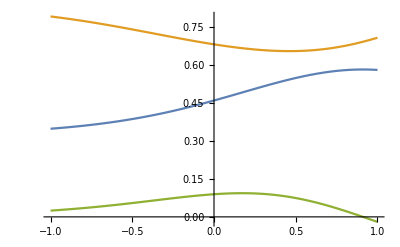

```mathematica
Plot[{XMnΓ[1,t,1,0],PMnΓ[1,t,1,0],DMnΓ[1,t,1,0]},{t,-1,1},PlotRange->All]
```

```mathematica
Jl[L_]:=KroneckerProduct[{{0,1},{-1,0}},IdentityMatrix[L]];
```

```mathematica
Jl[2]//MatrixForm
```

(0 | 0 | 1 | 0
0 | 0 | 0 | 1
-1 | 0 | 0 | 0
0 | -1 | 0 | 0)

```mathematica
Ω[tot_]:=SparseArray[{{x_,y_}/;x-y==-1&&OddQ[x]-> 1,{x_,y_}/;x-y==1&&OddQ[y]->-1},{2tot,2tot}]//Normal;
```

```mathematica
Ω[2]//MatrixForm
```

(0 | 1 | 0 | 0
-1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | -1 | 0)

```mathematica
XmnΓtabRex[ΓQ_,x_,ξI_,L_]:=XmnΓtabRex[ΓQ,x,ξI,L]=Module[{XmntabC},
XmntabC=Table[XmnΓ[ΓQ,x,ξI,m,n],{m,1,L},{n,1,L}];XmntabC]
```

```mathematica
PmnΓtabRex[ΓQ_,x_,ξI_,L_]:=PmnΓtabRex[ΓQ,x,ξI,L]=Module[{PmntabC},
PmntabC=Table[PmnΓ[ΓQ,x,ξI,m,n],{m,1,L},{n,1,L}];PmntabC]
```

```mathematica
DmnΓtabRex[ΓQ_,x_,ξI_,L_]:=DmnΓtabRex[ΓQ,x,ξI,L]=Module[{DmntabC},
DmntabC=Table[DmnΓ[ΓQ,x,ξI,m,n],{m,1,L},{n,1,L}];DmntabC]
```

```mathematica
(*Nice!*)
```

```mathematica
(*CmnΓtabRex3 is the correct thing to use.*)
```

```mathematica
ToeXMnΓ[ΓQ_, x_, ξI_, L_]:=ToeXMnΓ[ΓQ,x,ξI,L]=ToeplitzMatrix[Table[XMnΓ[ΓQ,x,ξI,Mn],{Mn,0,L-1}]];
```

```mathematica
ToePMnΓ[ΓQ_, x_, ξI_, L_]:=ToePMnΓ[ΓQ,x,ξI,L]=ToeplitzMatrix[Table[PMnΓ[ΓQ,x,ξI,Mn],{Mn,0,L-1}]];
```

```mathematica
ToeDMnΓ[ΓQ_, x_, ξI_, L_]:=ToeDMnΓ[ΓQ,x,ξI,L]=ToeplitzMatrix[Table[DMnΓ[ΓQ,x,ξI,Mn],{Mn,0,L-1}]];
```

```mathematica
CmnΓtabRex3[ΓQ_,x_,ξI_,L_]:=ArrayFlatten[{{ToeXMnΓ[ΓQ,x,ξI,L],ToeDMnΓ[ΓQ,x,ξI,L]},{ToeDMnΓ[ΓQ,x,ξI,L],ToePMnΓ[ΓQ,x,ξI,L]}}];
```

CoP as a Function of Subsystem Separation (Fixed Subsystem Size)

CoP as a Function of Subsystem Size (0 Separation)

CoP as a Function of Subsystem Size (Variable Separation)

CoP in the Continuum Limit?